# q q̄→μ μ in EW theory (SM ): GENERIC CHARGES

mass leptons MM!=0, box calculation

Confronto con EW_MM_naive per d=4 -> OK

### PROCESS:

```mathematica
CKM = IndexDelta;
Neglect[MU] = Neglect[MU2] = 0;
(*Neglect[MM] = Neglect[MM2] = 0;*)
process ={-F[3, {1}], F[3, {1}]} -> {-F[2, {2}], F[2, {2}]} ;

SetOptions[InsertFields,  Model -> "SM",InsertionLevel->{Particles}, Restrictions -> NoLightFHCoupling];
(*SetOptions[CalcFeynAmp,PaVeReduce->True];*)
(*SetOptions[CreateFeynAmp, GaugeRules -> {GaugeXi[Z] -> ZGAUGE, GaugeXi[A] -> AGAUGE,
 GaugeXi[W] -> WGAUGE} ];*)
```

## SM: Feynman rules and diagrams

Definisco valori di cariche e masse sostituite poi nei passaggi finali

```mathematica
CHARGESZl={QZLl->-1,QZUl->2/3,QZDl->-1/3,I3D->-1/2,I3L->-1/2,I3N->1/2,I3U->1/2};
CHARGESZr={QZLr->-1,QZUr->2/3,QZDr->-1/3};
CHARGESphl={QLl->-1,QUl->2/3,QDl->-1/3};
CHARGESphr={QLr->-1,QUr->2/3,QDr->-1/3};
MASSES={MU->0,MU2->0(*,MM->0,MM2->0,*),MD->0,MD2->0,S+T+U->2 MM2}
```

{MU→0,MU2→0,MD→0,MD2→0,S+T+U→2 MM2}

```mathematica
(*GENERALIZZAZIONE CARICHE/ISOSPIN PER CASO SM*)
coupling[x_]:=Module[{Mcouplin,chargenuZ,chargelepZ,chargeupZ,chargedownZ,n,m,chargenup,chargelep,chargedown,chargeup},

Mcouplin=M$CouplingMatrices;
(*____________________________  Z COUPLING  ______________________________*)
(*neutrino*)
chargenuZ[(lhs:C[_. F[1,{__}],_. F[1,{__}],_. V[2]])==rhs_]:=
lhs==(rhs/.{
	dZZZ1-> 2 I3N dZZZ1,
	1/(2 CW SW)->I3N/(CW SW),
	EL IndexDelta[j1_,j2_]->2*I3N*EL IndexDelta[j1,j2]
	

});
chargenuZ[other_]=other;
Mcouplin=chargenuZ/@Mcouplin;

(*lepton*)
chargelepZ[(lhs:C[_. F[2,{__}],_. F[2,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{-(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3L*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			SW/CW->-QZLl SW/CW,
			(-1/2+SW^2)->(I3L-QZLl*SW^2),
			dZAZ1->- QLl dZAZ1 (*CT misto gamma Z*)
			},
		rhsR/.{
		SW/CW->-QZLr SW/CW,
		dZAZ1->- QLr dZAZ1 (*CT misto gamma Z*)
		}
});
chargelepZ[other_]=other;
Mcouplin=chargelepZ/@Mcouplin;

(*q up*)
chargeupZ[(lhs:C[_. F[3,{__}],_. F[3,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3U*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			(1/2-2/3SW^2)->(I3U-QZUl*SW^2),
			
			dZAZ1->3/2 QUl dZAZ1,(*CT misto gamma Z: − δ [g1,g2] QU δZ(γZ)/2*)
			-2/3->-QZUl},
		rhsR/.{
			-dZAZ1 /3->-QUr*dZAZ1 /2, (*CT misto gamma Z*)
			-1/3 I*EL->-QZUr/2 I*EL,
			-2/3*I->-QZUr*I,
			-2/3->-QZUr,
			-SW /(3*CW)->-QZUr*SW /(2*CW)}
});
chargeupZ[other_]=other;
Mcouplin=chargeupZ/@Mcouplin;

(*q down*)
chargedownZ[(lhs:C[_. F[4,{__}],_. F[4,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{
			-(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3D*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			(-1/2+1/3 SW^2)->(I3D-QZDl*SW^2),
			dZAZ1->-3 QDl dZAZ1, (*CT misto gamma Z*)
			1/3->-QZDl},
			
		rhsR/.{
			dZZZ1->- 3 QZDr*dZZZ1 ,
			dZAZ1->- 3 QDr*dZAZ1 ,(*CT misto gamma Z*)
			1/3 I*EL->-QZDr I*EL,
			1/3*I->-QZDr*I,
			1/3->-QZDr,
			SW /(3*CW)->-QZDr*SW /(CW)}
});
chargedownZ[other_]=other;
Mcouplin=chargedownZ/@Mcouplin;

(*____________________________  GAMMA COUPLING  ___________________________*)
(*neutrino*)
chargenup[(lhs:C[_. F[1,{__}],_. F[1,{__}],_. V[1]])==rhs_]:=
lhs==(rhs/.{
		EL IndexDelta[j1_,j2_]->2*I3N*EL IndexDelta[j1,j2]
});
chargenup[other_]=other;
Mcouplin=chargenup/@Mcouplin;
(*lepton*)
chargelep[(lhs:C[_. F[2,{__}],_. F[2,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(-1/2+SW^2)->(I3L-QZLl*SW^2)/-QLl,(*CT misto gamma Z*)
			I->-QLl*I,
			1/2*I->-1/2 QLl*I
},
			
		rhsR/.{dZZA1->- QZLr dZZA1/-QLr,(*CT misto gamma Z*)
		I->-QLr*I,
			1/2*I->-1/2 QLr*I
		}
});
chargelep[other_]=other;
Mcouplin=chargelep/@Mcouplin;

(*q up*)
chargeup[(lhs:C[_. F[3,{__}],_. F[3,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(1/2-2/3SW^2)->(I3U-QZUl*SW^2),(*CT misto gamma Z*)
			-2/3->-QUl,
			-2/3*I->-QUl*I},
			
		rhsR/.{dZZA1->3/2 QZUr dZZA1,(*CT misto gamma Z*)
		-2/3->-QUr,
		-2/3*I->-QUr*I}
});
chargeup[other_]=other;
Mcouplin=chargeup/@Mcouplin;

(*q down*)
chargedown[(lhs:C[_. F[4,{__}],_. F[4,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(-1/2+1/3 SW^2)->(I3D-QZDl*SW^2),(*CT misto gamma Z*)
			1/3->-QDl,
			1/3*I->-QDl*I
			},
							
	rhsR/.{ dZZA1->-3 QZDr dZZA1,(*CT misto gamma Z*)
			1/3->-QDr,
			1/3*I->-QDr*I}
});
chargedown[other_]=other;
Mcouplin=chargedown/@Mcouplin;

Mcouplin
];
```

```mathematica
InitializeModel["SM",
ModelEdit :>{
M$ClassesDescription=M$ClassesDescription//.{(-Charge)->QL Charge,(2/3Charge)->QU Charge,(-1/3Charge)->QD Charge},
M$CouplingMatrices=coupling[M$CouplingMatrices]}

];
```

loading generic model file /home/arianna/Documenti/FeynArts-3.11/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/arianna/Documenti/FeynArts-3.11/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

## Feynman Diagrams

## Tree Level

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 18 field point(s)

in total: 2 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams



FeynArtsGraphics[][([1] | [2])]

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

in total: 2 Particles amplitudes

```mathematica
tops = CreateTopologies[0, 2 -> 2];
ins = InsertFields[tops, process];
Paint[ins,ColumnsXRows->{2,1},Numbering->Simple,
SheetHeader->None,ImageSize->{512,256}]
born1=CreateFeynAmp[ins];
```

## Self Energies

```mathematica
tops2 = CreateTopologies[1, 2 -> 2, SelfEnergiesOnly];
ins2 = InsertFields[tops2, process];
ins2 = DiagramSelect[ins2, FreeQ[#, Field[5|6] -> S]&];
Paint[ins2,ColumnsXRows->{11,7},Numbering->Simple,
SheetHeader->None,ImageSize->{1212,756}]
selfff=CreateFeynAmp[ins2];
```

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 10 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 65 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

Restoring 18 field point(s)

in total: 75 Particles insertions

> Top. 1 aebe/cfdf/egfggg.m, 0 diagrams

> Top. 2 aebe/cfdf/egfhghgh.m, 0 diagrams

-Graphics-

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5] | [6] | [7] | [8] | [9] | [10] | [11]
[12] | [13] | [14] | [15] | [16] | [17] | [18] | [19] | [20] | [21] | [22]
[23] | [24] | [25] | [26] | [27] | [28] | [29] | [30] | [31] | [32] | [33]
[34] | [35] | [36] | [37] | [38] | [39] | [40] | [41] | [42] | [43] | [44]
[45] | [46] | [47] | [48] | [49] | [50] | [51] | [52] | [53] | [54] | [55]
[56] | [57] | [58] | [59] | [60] | [61] | [62] | [63] | [64] | [65] | [66]
[67] | [68] | [69] | [70] | [71] | [72] | [73] | [74] | [75] | Null | Null)]

creating amplitudes at level(s) {Particles}

> Top. 1: 10 Particles amplitudes

> Top. 2: 65 Particles amplitudes

in total: 75 Particles amplitudes

## Vertices

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 8 Particles amplitudes

in total: 15 Particles amplitudes

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 7 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 8 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

> Top. 13: 0 Particles insertions

> Top. 14: 0 Particles insertions

> Top. 15: 0 Particles insertions

> Top. 16: 0 Particles insertions

> Top. 17: 0 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 0 Particles insertions

> Top. 20: 0 Particles insertions

> Top. 21: 0 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 0 Particles insertions

Restoring 18 field point(s)

in total: 15 Particles insertions

> Top. 1 aebe/cfdg/ehfgfhgh.m, 0 diagrams

> Top. 2 aebf/cgdg/ghefehfh.m, 0 diagrams

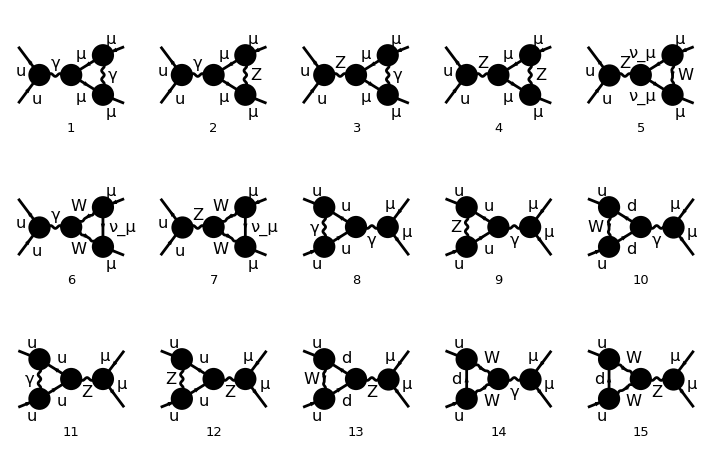

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5]
[6] | [7] | [8] | [9] | [10]
[11] | [12] | [13] | [14] | [15])]

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 8 Particles amplitudes

in total: 15 Particles amplitudes

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5]
[6] | [7] | [8] | [9] | [10]
[11] | [12] | [13] | [14] | [15])]

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 8 Particles amplitudes

in total: 15 Particles amplitudes

```mathematica
tops4 = CreateTopologies[1, 2 -> 2, TrianglesOnly];
ins4 = InsertFields[tops4, process];
ins4 = DiagramSelect[ins4, FreeQ[#, Field[5] -> S]&];
Paint[ins4,ColumnsXRows->{5,3},Numbering->Simple,
SheetHeader->None,ImageSize->{712,456}]
verttt=CreateFeynAmp[ins4];
```

## Boxes

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 4 Particles insertions

> Top. 8: 5 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

Restoring 18 field point(s)

in total: 9 Particles insertions

> Top. 1 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 2 aebf/cgdh/efehfggh.m, 0 diagrams

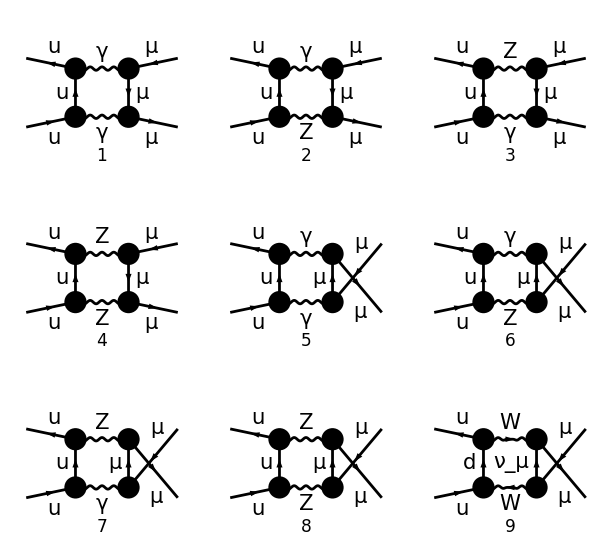

FeynArtsGraphics[][([1] | [2] | [3]
[4] | [5] | [6]
[7] | [8] | [9])]

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

> Top. 2: 5 Particles amplitudes

in total: 9 Particles amplitudes

```mathematica
tops5 = CreateTopologies[1, 2 -> 2, BoxesOnly];
ins5 = InsertFields[tops5, process];
Paint[ins5,ColumnsXRows->{3,3},Numbering->Simple,
SheetHeader->None,ImageSize->{612,556}]
box1=  CreateFeynAmp[ins5];
```

## Counterterms (CT)

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 2 Particles insertions

> Top. 8: 4 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

Restoring 18 field point(s)

in total: 8 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebe/cfdf/gegf.m, 0 diagrams

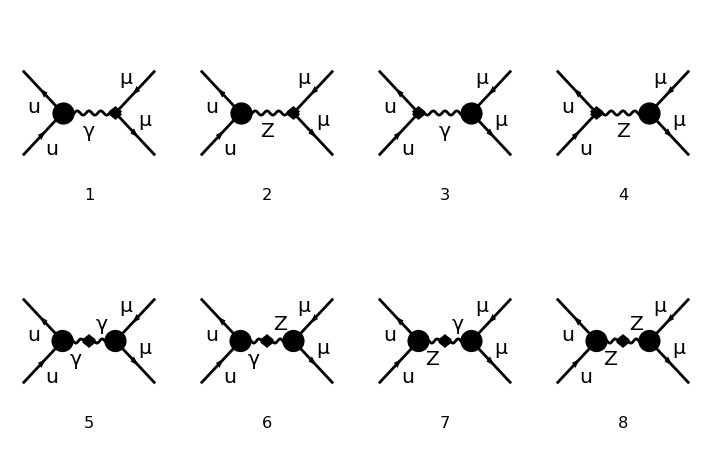

FeynArtsGraphics[][([1] | [2] | [3] | [4]
[5] | [6] | [7] | [8])]

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 2 Particles amplitudes

> Top. 3: 4 Particles amplitudes

in total: 8 Particles amplitudes

```mathematica
tops1 = CreateCTTopologies[1, 2 -> 2,
  ExcludeTopologies -> {TadpoleCTs,WFCorrectionCTs (*loop counterterms*)}];
ins1 = InsertFields[tops1, process];
Paint[ins1,ColumnsXRows->{4,2},Numbering->Simple,
SheetHeader->None,ImageSize->{712,456}]
counter = CreateFeynAmp[ins1];
```

## BOX

ampiezzabox . ampiezzaborn*

#### Classificazione

```mathematica
(*in input mettere box1*)
boxtable[box_]:=Module[{b1,b2,b3,samediag,b4,tden,uden,boxcl0,boxcl1},

(*primo metodo: topologie*)
b1=Table[
Which[MemberQ[Part[box,{i}][[1,1]],Topology==1,Infinity],T,
MemberQ[Part[box,{i}][[1,1]],Topology==2,Infinity],U,
True,Print["not identified"]],(*identificazione diagrammi t con particelle gamma/Z/W in base ai valori delle cariche negli stati finali, l'ordine è up,down. Il caso WW è per esclusione*)

{i,1,Length[box1]}];

(*secondo metodo*)
(*
tden=PropagatorDenominator[Plus[FourMomentum[Incoming,2],FourMomentum[Internal,1],Times[-1,FourMomentum[Outgoing,2]]],0];
uden=PropagatorDenominator[Plus[FourMomentum[Incoming,2],FourMomentum[Internal,1],Times[-1,FourMomentum[Outgoing,1]]],0];


boxcl0=Table[boxcl1[i]=Union[Cases[Part[box,{i}][[1,3]]/.MASSES,_FeynAmpDenominator,Infinity]/.FeynAmpDenominator->Sequence],
{i,1,Length[box]}];
Print[boxcl0];

b1=Table[
Which[MemberQ[boxcl1[i],tden,Infinity],T,
MemberQ[boxcl1[i],uden,Infinity],U,True,Null](*,
DeleteCases[boxcl1[i],uden|tden,Infinity]*),
{i,1,Length[box1]}];
*)
(*******************)

b2=Table[
Which[b1[[i]]===T,
{Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QZLl,Infinity],Z,
True,W],
Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QZLl,Infinity],Z,
True,W]},
b1[[i]]===U,

{Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QZLl,Infinity],Z,
True,W],
Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QZLl,Infinity],Z,
True,W]}
,
True,Print["not identified"]](*identificazione diagrammi t con topology 1 e u con topology 2*)
,(*identificazione diagrammi t con particelle gamma/Z/W in base ai valori delle cariche negli stati finali, l'ordine è up,down. Il caso WW è per esclusione*)

{i,1,Length[box]}];
b3=Table[{i,b1[[i]],b2[[i]]},{i,1,Length[box]}];
Print[b3];
samediag=Gather[b3,Last[#1]==Last[#2]&];
b4=Table[{couple[i]==Last[samediag[[i,1]]],bbox[i]=Cases[samediag[[i]],_Integer,{2}]},{i,1,Length[samediag]}];(*couples:diag t , diag u*)


b4
];
```

```mathematica
boxtable[box1]
```

{{1,T,{γ,γ}},{2,T,{γ,Z}},{3,T,{Z,γ}},{4,T,{Z,Z}},{5,U,{γ,γ}},{6,U,{γ,Z}},{7,U,{Z,γ}},{8,U,{Z,Z}},{9,U,{W,W}}}

{{couple[1]=={γ,γ},{1,5}},{couple[2]=={γ,Z},{2,6}},{couple[3]=={Z,γ},{3,7}},{couple[4]=={Z,Z},{4,8}},{couple[5]=={W,W},{9}}}

```mathematica
Table[totbbox[i]={Part[box1,{bbox[i][[1]]}][[1,3]],Part[box1,{bbox[i][[2]]}][[1,3]]},{i,1,4}];
totbbox[5]=Part[box1,{bbox[5][[1]]}][[1,3]];
```

```mathematica
(*set variabili semplificate*)
mzg=Times[MZ,Power[ZGAUGE,Rational[1,2]]];
mwg=Times[MW,Power[WGAUGE,Rational[1,2]]];
P1=FourMomentum[Incoming,1];
P2=FourMomentum[Incoming,2];
Q1=FourMomentum[Internal,1];
K1=FourMomentum[Outgoing,1];
K2=FourMomentum[Outgoing,2];
```

### Caso box generico:

METTERE MANUALMENTE: totbbox[i] e 1 per fotone e 2 per z per born diagram

```mathematica
tboxzz=totbbox[4][[1]]//.MASSES//.{DiracSpinor[Times[-1,P1],x_]->DiracSpinor[P1,x],DiracSpinor[Times[-1,K1],x_]->DiracSpinor[K1,x]};
uboxzz=totbbox[4][[2]]//.MASSES//.{DiracSpinor[Times[-1,P1],x_]->DiracSpinor[P1,x],DiracSpinor[Times[-1,K1],x_]->DiracSpinor[K1,x]};
wwbox=totbbox[5]//.MASSES//.{DiracSpinor[Times[-1,P1],x_]->DiracSpinor[P1,x],DiracSpinor[Times[-1,K1],x_]->DiracSpinor[K1,x]};
```

```mathematica
tboxzz=tboxzz/.FourMomentum[Internal,1]->Times[-1,FourMomentum[Internal,1]]
uboxzz=uboxzz/.FourMomentum[Internal,1]->Times[-1,FourMomentum[Internal,1]]
wwbox=wwbox/.FourMomentum[Internal,1]->Times[-1,FourMomentum[Internal,1]];
```

1/(16 π^4)ⅈ v̄[p1,0].((ⅈ EL (I3U-QZUl SW2) ga[Lor1].om_-)/(CW SW)-(ⅈ EL QZUr SW ga[Lor1].om_+)/CW).gs[q1].((ⅈ EL (I3U-QZUl SW2) IndexDelta[Col1,Col2] ga[Lor3].om_-)/(CW SW)-(ⅈ EL QZUr SW IndexDelta[Col1,Col2] ga[Lor3].om_+)/CW).u[p2,0] ū[k2,MM].((ⅈ EL (I3L-QZLl SW2) ga[Lor4].om_-)/(CW SW)-(ⅈ EL QZLr SW ga[Lor4].om_+)/CW).(MM+gs[-(p2)+q1+k2]).((ⅈ EL (I3L-QZLl SW2) ga[Lor2].om_-)/(CW SW)-(ⅈ EL QZLr SW ga[Lor2].om_+)/CW).v[k1,MM] FeynAmpDenominator[1/(-MZ2+(p2-q1)^2),1/(q1)^2,1/(-MM2+(p2-q1-k2)^2),1/(-MZ2+(p2-q1-k1-k2)^2)] g[Lor1,Lor2] g[Lor3,Lor4] SumOver[Col1,3,External] SumOver[Col2,3,External]

1/(16 π^4)ⅈ v̄[p1,0].((ⅈ EL (I3U-QZUl SW2) ga[Lor1].om_-)/(CW SW)-(ⅈ EL QZUr SW ga[Lor1].om_+)/CW).gs[q1].((ⅈ EL (I3U-QZUl SW2) IndexDelta[Col1,Col2] ga[Lor3].om_-)/(CW SW)-(ⅈ EL QZUr SW IndexDelta[Col1,Col2] ga[Lor3].om_+)/CW).u[p2,0] ū[k2,MM].((ⅈ EL (I3L-QZLl SW2) ga[Lor2].om_-)/(CW SW)-(ⅈ EL QZLr SW ga[Lor2].om_+)/CW).(MM+gs[p2-q1-k1]).((ⅈ EL (I3L-QZLl SW2) ga[Lor4].om_-)/(CW SW)-(ⅈ EL QZLr SW ga[Lor4].om_+)/CW).v[k1,MM] FeynAmpDenominator[1/(-MZ2+(p2-q1)^2),1/(q1)^2,1/(-MM2+(p2-q1-k1)^2),1/(-MZ2+(p2-q1-k1-k2)^2)] g[Lor1,Lor2] g[Lor3,Lor4] SumOver[Col1,3,External] SumOver[Col2,3,External]

```mathematica
(*confronto Nar*)
tboxzz=tboxzz/.{Q1->-(Q1-P1)}//.{-P1-P2+K2->-K1,P1+P2-K2->K1}
uboxzz=uboxzz/.{Q1->(Q1-P2)}//.2P2-Q1->Q1//.Q1-K1-K2->-Q1+P1+P2//.PropagatorDenominator[Q1-K1,x_]->PropagatorDenominator[-Q1+K1,x]//.PropagatorDenominator[Q1-P2,x_]->PropagatorDenominator[-Q1+P2,x]
```

1/(16 π^4)ⅈ v̄[p1,0].(-ⅈ EL QUl ga[Lor1].om_--ⅈ EL QUr ga[Lor1].om_+).gs[-(p1)+q1].(-ⅈ EL QUl IndexDelta[Col1,Col2] ga[Lor3].om_--ⅈ EL QUr IndexDelta[Col1,Col2] ga[Lor3].om_+).u[p2,0] ū[k2,MM].(-ⅈ EL QLl ga[Lor4].om_--ⅈ EL QLr ga[Lor4].om_+).(MM+gs[q1-k1]).(-ⅈ EL QLl ga[Lor2].om_--ⅈ EL QLr ga[Lor2].om_+).v[k1,MM] FeynAmpDenominator[1/(p1-q1)^2,1/(p1+p2-q1)^2,1/(q1)^2,1/(-MM2+(-(q1)+k1)^2)] g[Lor1,Lor2] g[Lor3,Lor4] SumOver[Col1,3,External] SumOver[Col2,3,External]

1/(16 π^4)ⅈ v̄[p1,0].(-ⅈ EL QUl ga[Lor1].om_--ⅈ EL QUr ga[Lor1].om_+).gs[p2-q1].(-ⅈ EL QUl IndexDelta[Col1,Col2] ga[Lor3].om_--ⅈ EL QUr IndexDelta[Col1,Col2] ga[Lor3].om_+).u[p2,0] ū[k2,MM].(-ⅈ EL QLl ga[Lor2].om_--ⅈ EL QLr ga[Lor2].om_+).(MM+gs[q1-k1]).(-ⅈ EL QLl ga[Lor4].om_--ⅈ EL QLr ga[Lor4].om_+).v[k1,MM] FeynAmpDenominator[1/(p2-q1)^2,1/(p1+p2-q1)^2,1/(q1)^2,1/(-MM2+(-(q1)+k1)^2)] g[Lor1,Lor2] g[Lor3,Lor4] SumOver[Col1,3,External] SumOver[Col2,3,External]

```mathematica
(*funzione per semplificare propagatori*)
numer[x__ PropagatorDenominator[p_,MZ] PropagatorDenominator[p_,mzg]]:=numer[x/(MZ^2-mzg^2)(PropagatorDenominator[p,MZ]-PropagatorDenominator[p,mzg])];
numerw[x__ PropagatorDenominator[p_,MW] PropagatorDenominator[p_,mwg]]:=numerw[x/(MW^2-mwg^2)(PropagatorDenominator[p,MW]-PropagatorDenominator[p,mwg])];
```

```mathematica
(*BORN*)
born=Part[born1,{2}][[1,3]]//.{Index[Lorentz, 1]->Index[Lorentz, bn1],
Index[Lorentz, 2]->Index[Lorentz, bn2]}//.MASSES//.{DiracSpinor[Times[-1,P1],x_]->DiracSpinor[P1,x],DiracSpinor[Times[-1,K1],x_]->DiracSpinor[K1,x]};
bornchains=DeleteCases[Cases[born,_FermionChain,Infinity],_IndexDelta,Infinity];
conjbornchains=CONJ/@Reverse[bornchains,{2}]/.{I->-I,-I->I}
(*colour matrix*)
colourborn=Union[Cases[born,_SumOver|_IndexDelta,Infinity]]
(*born propagators*)
bornpropag=DeleteCases[born, _SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times;
bornpropag2=Collect[numer/@%/.numer->Sequence//Simplify,
PropagatorDenominator[x_,mzg],Simplify]//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)
```

{CONJ[v̄[p2,0].(-(ⅈ EL (I3U-QZUl SW2) ga[Lorbn1].om_-)/(CW SW)+(ⅈ EL QZUr SW ga[Lorbn1].om_+)/CW).u[p1,0]],CONJ[ū[k1,MM].(-(ⅈ EL (I3L-QZLl SW2) ga[Lorbn2].om_-)/(CW SW)+(ⅈ EL QZLr SW ga[Lorbn2].om_+)/CW).v[k2,MM]]}

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

SP[Lorbn1,Lorbn2]/(-MZ2+(k1+k2)^2)

```mathematica
(*LOOP DIAGRAM*)

colourf[diag_]:=Module[{input2,fermionchain},
diagram=diag;
(*trace closed fermion loop(if any)*)
tr=Cases[diagram,_MatrixTrace,Infinity];
(*fermionchain without tr and with external particles masses->0*)
input2=DeleteCases[diagram,_MatrixTrace,Infinity]//.MASSES;
fermionchain=Cases[input2,_FermionChain,Infinity];
(*colour traces*)
sunt=Cases[Collect[fermionchain,_SUNT,Simplify],_SUNT| _IndexDelta,Infinity];
trsunt=Cases[Collect[tr,_SUNT,Simplify],_SUNT| _IndexDelta,Infinity];(*SUNT in tr*)
sumover=Cases[input2,_SumOver,Infinity];
colour=Join[sunt,trsunt,sumover,colourborn];

colour
];
```

```mathematica
colourf[tboxzz]
colourf[uboxzz]
colourf[wwbox]
colourf[Part[selfff,{4}]]
```

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External],IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External],IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External],IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

«1 more identical outputs»

#### Semplificazione propagatori

Divisione in termini dipendenti da gauge e indipendenti

```mathematica
(*box t*)
tnumerat=DeleteCases[tboxzz, _MatrixTrace |_SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times//Simplify
(*box u*)
unumerat=DeleteCases[uboxzz, _MatrixTrace |_SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times//Simplify
(*box w*)
wnumerat=DeleteCases[wwbox, _MatrixTrace |_SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times//Simplify
```

(ⅈ g[Lor1,Lor2] g[Lor3,Lor4] 1/(-MZ2+(p2-q1)^2) 1/(q1)^2 1/(-MM2+(p2-q1-k2)^2) 1/(-MZ2+(p2-q1-k1-k2)^2))/(16 π^4)

(ⅈ g[Lor1,Lor2] g[Lor3,Lor4] 1/(-MZ2+(p2-q1)^2) 1/(q1)^2 1/(-MM2+(p2-q1-k1)^2) 1/(-MZ2+(p2-q1-k1-k2)^2))/(16 π^4)

(ⅈ g[Lor1,Lor2] g[Lor3,Lor4] 1/(-MW2+(p2-q1)^2) 1/(q1)^2 1/(p2-q1-k1)^2 1/(-MW2+(p2-q1-k1-k2)^2))/(16 π^4)

```mathematica
(*prove semplificaz propagatore generico*)
sempp[propag_]:=Module[{t1,t11,t111,t1111,t2,t22,t222,t2222,tnumerat1,tnumerat2,t1w,t11w,t111w,t1111w,t2w,t22w,t222w,t2222w,tnumerat1w,tnumerat2w},
propagatore=propag;
tnn=Select[propagatore,MemberQ[#,ZGAUGE|MZ,Infinity]&];(*seleziona i termini contenenti ZGAUGE oppure massa MZ*)
tnn2=Select[propagatore,FreeQ[#,ZGAUGE|MZ,Infinity]&];(*seleziona i termini restanti, passaggio intermedio*)
	tnnw=Select[tnn2,MemberQ[#,WGAUGE|MW,Infinity]&];(*seleziona i termini contenenti WGAUGE oppure massa MW in tnn2*)
	tnnrest=Select[tnn2,FreeQ[#,WGAUGE|MW,Infinity]&];(*seleziona i termini restanti*)
(*propagatore=tnn*tnnw*tnnrest*)

(*ZGAUGE*)
Which[Length[tnn]===2,(*caso di diagrammi con γ e Z*)
	t1=tnn//Expand;
	t11=numer/@t1/.numer->Sequence//Simplify;
	t111=Collect[t11,PropagatorDenominator[x_,mzg],FullSimplify]//.ZGAUGE->Zm1+1//.FourVector[a__]:>Distribute[FourVector[a]];
	t1111=Collect[t111,Zm1,Simplify]//.FourVector[a__,b_]-FourVector[a__,b_]->0//.Zm1->ZGAUGE-1;
	tnumerat1=t1111//.FourVector[a_, Index[w__]]+FourVector[b_, Index[w__]] ->FourVector[a + b, Index[w]];
	totnum=tnumerat1,

	Length[tnn]>2,(*caso con 2 Z*)
		t1=tnn[[1;;Length[tnn]/2]]//Expand;
		t11=numer/@t1/.numer->Sequence//Simplify;
		t111=Collect[t11,PropagatorDenominator[x_,mzg],FullSimplify]//.ZGAUGE->Zm1+1//.FourVector[a__]:>Distribute[FourVector[a]];
		t1111=Collect[t111,Zm1,Simplify]//.FourVector[a__,b_]-FourVector[a__,b_]->0//.Zm1->ZGAUGE-1;
		tnumerat1=t1111//.FourVector[a_, Index[w__]]+FourVector[b_, Index[w__]]->FourVector[a + b, Index[w]];

		t2=tnn[[Length[tnn]/2+1;;Length[tnn]]]//Expand;
		t22=numer/@t2/.numer->Sequence//Simplify;
		t222=Collect[t22,PropagatorDenominator[x_,mzg],FullSimplify]//.ZGAUGE->Zm1+1//.FourVector[a__]:>Distribute[FourVector[a]];
		t2222=Collect[t222,Zm1,Simplify]//.FourVector[a__,b_]-FourVector[a__,b_]->0//.Zm1->ZGAUGE-1;
		tnumerat2=t2222//.FourVector[a_, Index[w__]]+FourVector[b_, Index[w__]]->FourVector[a + b, Index[w]];
		totnum=tnumerat1*tnumerat2,

	True,
		totnum=1];

(*WGAUGE*)
Which[Length[tnnw]===2,(*caso di diagrammi con un solo W*)
		t1w=tnnw//Expand;
		t11w=numerw/@t1w/.numerw->Sequence//Simplify;
		t111w=Collect[t11w,PropagatorDenominator[x_,mwg],FullSimplify]//.ZGAUGE->Zm1+1//.FourVector[a__]:>Distribute[FourVector[a]];
		t1111w=Collect[t111w,Zm1,Simplify]//.FourVector[a__,b_]-FourVector[a__,b_]->0//.Zm1->ZGAUGE-1;
		tnumerat1w=t1111w//.FourVector[a_, Index[w__]]+FourVector[b_, Index[w__]] ->FourVector[a + b, Index[w]];
		totnum1=tnumerat1w,

	Length[tnnw]>2,(*caso con 2 W*)
		t1w=tnnw[[1;;Length[tnnw]/2]]//Expand;
		t11w=numerw/@t1w/.numerw->Sequence//Simplify;
		t111w=Collect[t11w,PropagatorDenominator[x_,mwg],FullSimplify]//.WGAUGE->Zm1+1//.FourVector[a__]:>Distribute[FourVector[a]];
		t1111w=Collect[t111w,Zm1,Simplify]//.FourVector[a__,b_]-FourVector[a__,b_]->0//.Zm1->WGAUGE-1;
		tnumerat1w=t1111w//.FourVector[a_, Index[w__]]+FourVector[b_, Index[w__]] ->FourVector[a + b, Index[w]];

	t2w=tnnw[[Length[tnnw]/2+1;;Length[tnnw]]]//Expand;
	t22w=numerw/@t2w/.numerw->Sequence//Simplify;
	t222w=Collect[t22w,PropagatorDenominator[x_,mwg],FullSimplify]//.WGAUGE->Zm1+1//.FourVector[a__]:>Distribute[FourVector[a]];
	t2222w=Collect[t222w,Zm1,Simplify]//.FourVector[a__,b_]-FourVector[a__,b_]->0//.Zm1->WGAUGE-1;
	tnumerat2w=t2222w//.FourVector[a_, Index[w__]]+FourVector[b_, Index[w__]] ->FourVector[a + b, Index[w]];
	totnum1=tnumerat1w*tnumerat2w,

	True,
		totnum1=1];


propagtot=totnum*totnum1*tnnrest];
```

```mathematica
tpropag=sempp[tnumerat]
upropag=sempp[unumerat]
wpropag=sempp[wnumerat]
```

(ⅈ g[Lor1,Lor2] g[Lor3,Lor4] 1/(-MZ2+(p2-q1)^2) 1/(q1)^2 1/(-MM2+(p2-q1-k2)^2) 1/(-MZ2+(p2-q1-k1-k2)^2))/(16 π^4)

(ⅈ g[Lor1,Lor2] g[Lor3,Lor4] 1/(-MZ2+(p2-q1)^2) 1/(q1)^2 1/(-MM2+(p2-q1-k1)^2) 1/(-MZ2+(p2-q1-k1-k2)^2))/(16 π^4)

(ⅈ g[Lor1,Lor2] g[Lor3,Lor4] 1/(-MW2+(p2-q1)^2) 1/(q1)^2 1/(p2-q1-k1)^2 1/(-MW2+(p2-q1-k1-k2)^2))/(16 π^4)

```mathematica
nn=7;
denomt=tnumerat[[nn]]/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)
denomu=unumerat[[nn]]/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)
```

1/(-MM2+(p2-q1-k2)^2)

1/(-MM2+(p2-q1-k1)^2)

```mathematica
(*propagatore born*)
bornpropag2
(*propagatore box, parte in comune fra t e u. propagatore box W*)

propagatT=tnumerat[[nn]];
propagatU=unumerat[[nn]];

ptot=DeleteCases[tpropag,propagatT,Infinity]+DeleteCases[upropag,propagatU,Infinity]//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)
ptotw=DeleteCases[wpropag,propagatU,Infinity]//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)
```

SP[Lorbn1,Lorbn2]/(-MZ2+(k1+k2)^2)

(ⅈ SP[Lor1,Lor2] SP[Lor3,Lor4])/(8 π^4 (-MZ2+(p2-q1)^2) (q1)^2 (-MZ2+(p2-q1-k1-k2)^2))

(ⅈ SP[Lor1,Lor2] SP[Lor3,Lor4])/(16 π^4 (-MW2+(p2-q1)^2) (q1)^2 (p2-q1-k1)^2 (-MW2+(p2-q1-k1-k2)^2))

#### Trace

```mathematica
(*  naive anticommuting gamma5 definitions   *)
myTr[a_,b_] := 4 SP[a,b];
myTr[x__] := Module[{lista,ultima,menouno,menodue,coefficienti,nuovetracce,
                     risultato, i},
		    lista = {x};
                    ultima = lista[[-1]];
		    menouno = Delete[lista,-1];
		    menodue = Table[ Delete[ menouno, i], {i,1,Length[menouno]}];
		    coefficienti = Table[ (-1)^(i+1) SP[ultima,menouno[[i]] ],
                                          {i,1,Length[menouno]}];
		    nuovetracce = Map[ Apply[ myTr, # ] &, menodue];

                    risultato = coefficienti.nuovetracce;
                    risultato
 ] /; FreeQ[{x},G5] ;
```

```mathematica
myTr[G5,G5] = 4;
myTr[z___,-G5]:=-myTr[z,G5];
myTr[s___,MM,u___]:=MM myTr[s,u];
myTr[x_,G5] = 0;
myTr[x_,y_,G5] = 0;
myTr[x_,y_,z_,G5] = 0;
myTr[x__,G5] := 0 /; OddQ[Length[{x}]] && FreeQ[{x},G5] ;
myTr[a___,G5,b___,G5,c___] := (-1)^Length[{b}]*myTr[a,b,c] /; FreeQ[{b},G5] ;
myTr[a___,G5,b__] := (-1)^Length[{b}]*myTr[a,b,G5] /; FreeQ[Union[{a},{b}],G5] ;
myTr[a1_,a2_,a3_,a4_,G5] =- 4 I myEps[a1,a2,a3,a4];
myTr[x___,a1_,a2_,a3_,a4_,a5_,a6_,G5] := Module[ {lista,ultima,menouno,menodue,coefficienti,nuovetracce,
                     risultato, i},
  index = Unique[a];
  risultato = myTr[x,a1,a2,a3,a6,G5] SP[a4,a5]-
              myTr[x,a1,a2,a3,a5,G5] SP[a4,a6]+
              myTr[x,a1,a2,a3,a4,G5] SP[a5,a6]+
  I  myTr[x,a1,a2,a3,DiracMatrix[Index[Lorentz,index]]] myEps[a4,a5,a6,DiracMatrix[Index[Lorentz,index]]]; 
  risultato
 ]  /; FreeQ[Union[{x},{a1,a2,a3,a4,a5,a6}],G5] ;
```

```mathematica
(*funzioni prodotto scalare e levicivita*)
SetAttributes[SP,Orderless];
SP/:SP[Index[u__],Index[v__]] SP[p_,Index[u__]] := SP[p,Index[v]];
SP/:SP[a_,Index[mu__]]^2 := SP[a,a];
SP/:SP[a_,Index[mu__]] SP[b_,Index[mu__]] := SP[a,b];
SP/:SP[Index[mu__],Index[mu__]] = d;
SP/:SP[Index[mu__],Index[nu__]]^2 = d;
SP/:SP[-b_,a_]:=-SP[b,a];
SP/:SP[DiracSlash[w_],x_]:=SP[w,x];
SP/:SP[DiracMatrix[w_],x_]:=SP[w,x];
(*levicivita product. 4 indices (d->4)*)
myEps/:myEps[a__]^2:=-Expand@Det@Outer[SP,{a},{a}];
myEps/:myEps[a__] myEps[b__]:=-Expand@Det@Outer[SP,{a},{b}];
```

```mathematica
SP/:SP[P1,P1]:=0;
SP/:SP[P2,P2]:=0;
SP/:SP[K2,K2]:=MM2;
SP/:SP[K1,K1]:=MM2;
```

```mathematica
SP/:SP[P1,P2]:=S/2;
SP/: SP[K1,K2]:=S/2-MM2;
SP/: SP[P1,K1]:=(MM2-T)/2;
SP/: SP[P2,K2]:=(MM2-T)/2; 
SP/:SP[P1,K2]:=(MM2-U)/2; SP/:SP[P2,K1]:=(MM2-U)/2;
```

```mathematica
(*PROPRIETÀ MYEPS*)
myEps /: myEps[a___,Index[Lorentz,mu_],b___] SP[p_,Index[Lorentz,mu_]] := myEps[a,p,b]; 
myEps[a___,b_,c___,b_,d___] := 0
```

```mathematica
move2[a___,ChiralityProjector[pm_],dm:MM|-MM,b___]:=move2[a,dm,ChiralityProjector[pm],b];
move2[a___,ChiralityProjector[pm_],dm:_DiracMatrix|_DiracSlash,b___]:=move2[a,dm,ChiralityProjector[-pm],b];
move2[a___,ChiralityProjector[x_],ChiralityProjector[y_],b___]:=0/;x≠y;
move2[a___,ChiralityProjector[x_],ChiralityProjector[y_],b___]:=move2[a,ChiralityProjector[x],b]/;x==y;
(*NOTA: ANTICOMMUTAZIONE IN D-DIMENSIONI *)
```

```mathematica
trr[s___,MM,u___]:=MM trr[s,u];
trr[s___,-MM,u___]:=-MM trr[s,u];
```

```mathematica
(*calcolo traccia*)
traces[statoi_,statof_]:=Module[{tr0f,tr1i,tr2i,tr3i,tr1f,tr2f,tr3f},

(*trace:*)
traceff4[x___, DiracSpinor[z:K2|P2,w_], DiracSpinor[z:K2|P2,w_],y___]:=traceff4[x,(DiracSlash[z]+w),y];
traceff4[ DiracSpinor[z:K2|P2,w_],x__,DiracSpinor[z:K2|P2,w_]]:=traceff4[(DiracSlash[z]+w),x];
traceff4[x___, DiracSpinor[z:K1|P1,w_], DiracSpinor[z:K1|P1,w_],y___]:=traceff4[x,(DiracSlash[z]-w),y];
traceff4[ DiracSpinor[z:K1|P1,w_],x__,DiracSpinor[z:K1|P1,w_]]:=traceff4[(DiracSlash[z]-w),x];
traceff4[a___,-G5,b___]:=- traceff4[a,G5,b];

move2[a___,1,b___]:=move2[a,b];
(*stato i*)
tr1i=Table[traceff4[statoi[[i]]/.List->Sequence],{i,1,Length[statoi]}]//.traceff4->move2;(*sposto proiettori in fondo*)
tr2i=Map[Distribute,1/2 DeleteCases[tr1i,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},Infinity];(*sostituisco om+- con espressioni G5 esplicite*)
tr3i=tr2i//.move2->myTr/.{DiracMatrix->Sequence,DiracSlash->Sequence}//Expand;(*espando e calcolo traccia*)

Print["stato i ",1/2 DeleteCases[tr1i,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)}];

(*stato f*)
tr0f=Table[traceff4[statof[[i]]/.List->Sequence],{i,1,Length[statof]}];
tr1f=Replace[Table[{Distribute[tr0f[[i]]]},{i,1,Length[tr0f]}],Plus->Sequence,{2},Heads->True]//.traceff4->move2;
tr2f=Flatten[Map[Distribute,1/2 DeleteCases[tr1f,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},Infinity]];
tr3f=tr2f//.move2->trr//.trr->myTr/.{DiracMatrix->Sequence,DiracSlash->Sequence}//Expand;

Print["stato f ",1/2 DeleteCases[tr1f,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)}];

Return[{tr3i,tr3f}]

];
```

```mathematica
(*input->diag=loop diagram *)
fermiontrace[diag_]:=Module[{tborn1,tborn2,hb,hbc,tborn3i,tborn3ic,tborn3f,tborn3fc,fermionchain,sti,sti1,tbi,tbic,tbi2,tbi3,tbi3c,stf,stf1,tbf,tbfc,tbf2,tbf3,tbf3c},
(*****BORN*****)
tborn1=Table[Map[Distribute,conjbornchains,3][[i]],{i,1,2}];
tborn2=Apply[List,tborn1,{1}]/.CONJ->Sequence;
(*seleziono termini per calcolo traccia e cariche*)
hb=Table[Table[Cases[tborn2[[j,i]],_NonCommutative,Infinity],{i,1,Length[tborn2[[j]]]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence,{j,1,2}];
hbc=Table[Table[DeleteCases[tborn2[[j,i]],_NonCommutative,Infinity],{i,1,Length[tborn2[[j]]]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence,{j,1,2}];
(*STATO I*)
tborn3i=Flatten[Select[hb,MemberQ[#,DiracSpinor[P1,_],Infinity]&],1];
tborn3ic=Flatten[Select[hbc,MemberQ[#,QZUl|QUl,Infinity]&],1];(*charges/coupling*)
(*STATO F*)
tborn3f=Flatten[Select[hb,MemberQ[#,DiracSpinor[K1,_],Infinity]&],1];
tborn3fc=Flatten[Select[hbc,MemberQ[#,QZLl|QLl,Infinity]&],1];(*charges/coupling*)

(*****LOOP DIAGRAM*****)
(*trace closed fermion loop(if any)*)
tr=Cases[diag,_MatrixTrace,Infinity];
(*fermionchain without tr and with external particles masses->0*)
input=DeleteCases[diag,_MatrixTrace,Infinity]//.MASSES;
(*fermionchain part for trace computation*)
fermionchain=DeleteCases[Cases[input,_FermionChain,Infinity],_SUNT|_IndexDelta,Infinity];
(*select fermionchain, expand sums, split state i/f*)
tab1=Table[Distribute[fermionchain[[i]]],{i,1,2}];
(*STATO I*)
sti=Select[tab1,MemberQ[#,DiracSpinor[P1,_],Infinity]&];(*select stato i*)
If[MemberQ[sti,Plus[FermionChain[__],_],Infinity],sti1=Flatten[Apply[List,sti,{1}],1],sti1=sti];(*suddivide in lista se ha piu elementi*)
(*seleziono termini per calcolo traccia e cariche*)
tbi=Table[Cases[sti1[[i]],_NonCommutative,Infinity],{i,1,Length[sti1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbic=Table[DeleteCases[sti1[[i]],_NonCommutative,Infinity],{i,1,Length[sti1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;

tbi2=Table[move2@@tbi[[i]],{i,1,Length[tbi]}]//.move2->List;(*sposto proiettori in fondo a destra con anticommutazione*)
tbi3=DeleteCases[tbi2,0,1];
tbi3c=Delete[tbic,Position[tbi2,0,{1}]];(*semplificazione se ci sono dei termini nulli dove ho om- om+ *)
(*union diag*born*)
stati=Flatten[Table[{Join[tbi3[[i]],tborn3i[[1]]],Join[tbi3[[i]],tborn3i[[2]]]},{i,1,Length[tbi3]}],1];
chi=Flatten[Table[{Join[tbi3c[[i]],tborn3ic[[1]]],Join[tbi3c[[i]],tborn3ic[[2]]]},{i,1,Length[tbi3c]}],1]//.FermionChain->Times;

(*STATO F*)(*procedimento analogo a STATO I*)
stf=Select[tab1,MemberQ[#,DiracSpinor[K2,_],Infinity]&];
If[MemberQ[stf,Plus[FermionChain[__],_],Infinity],stf1=Flatten[Apply[List,stf,{1}],1],stf1=stf];
tbf=Table[Cases[stf1[[i]],_NonCommutative,Infinity],{i,1,Length[stf1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbfc=Table[DeleteCases[stf1[[i]],_NonCommutative,Infinity],{i,1,Length[stf1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbf2=Replace[Table[Distribute[tbf[[i]]//.List->f],{i,1,Length[tbf]}],Plus->Sequence,{2},Heads->True]//.f->move2;
tbf3=DeleteCases[tbf2,0,1]//.move2->List;
If[FreeQ[tbf2,MM,Infinity],
tbf3c=Delete[tbfc,Position[tbf2,0,{1}]],
tbf3c=tbfc];(*semplificazione se ci sono dei termini nulli dove ho om- om+ *)
statf=Flatten[Table[{Join[tbf3[[i]],tborn3f[[1]]],Join[tbf3[[i]],tborn3f[[2]]]},{i,1,Length[tbf3]}],1];
chf=Flatten[Table[{Join[tbf3c[[i]],tborn3fc[[1]]],Join[tbf3c[[i]],tborn3fc[[2]]]},{i,1,Length[tbf3c]}],1]//.FermionChain->Times;

Print["trace closed fermion loop(if any): ",tr];
Return[{stati,statf}]
];
```

```mathematica
boxtt=traces[fermiontrace[tboxzz][[1]],fermiontrace[tboxzz][[2]]];
```

trace closed fermion loop(if any): {}

trace closed fermion loop(if any): {}

stato i {1/2 move2[gs[p1],ga[Lor1],gs[q1],ga[Lor3],gs[p2],ga[Lorbn1],1-G5],1/2 move2[gs[p1],ga[Lor1],gs[q1],ga[Lor3],gs[p2],ga[Lorbn1],1+G5]}

stato f {{1/2 (move2[MM,ga[Lor4],gs[-(p2)+q1+k2],ga[Lor2],gs[k1],ga[Lorbn2],1-G5]+move2[gs[k2],ga[Lor4],gs[-(p2)+q1+k2],ga[Lor2],gs[k1],ga[Lorbn2],1-G5])},{1/2 (move2[MM,ga[Lor4],gs[-(p2)+q1+k2],ga[Lor2],-MM,ga[Lorbn2],1+G5]+move2[gs[k2],ga[Lor4],gs[-(p2)+q1+k2],ga[Lor2],-MM,ga[Lorbn2],1+G5])},{1/2 (move2[MM,ga[Lor4],MM,ga[Lor2],-MM,ga[Lorbn2],1-G5]+move2[gs[k2],ga[Lor4],MM,ga[Lor2],-MM,ga[Lorbn2],1-G5])},{1/2 (move2[MM,ga[Lor4],MM,ga[Lor2],gs[k1],ga[Lorbn2],1+G5]+move2[gs[k2],ga[Lor4],MM,ga[Lor2],gs[k1],ga[Lorbn2],1+G5])},{1/2 (move2[MM,ga[Lor4],MM,ga[Lor2],gs[k1],ga[Lorbn2],1-G5]+move2[gs[k2],ga[Lor4],MM,ga[Lor2],gs[k1],ga[Lorbn2],1-G5])},{1/2 (move2[MM,ga[Lor4],MM,ga[Lor2],-MM,ga[Lorbn2],1+G5]+move2[gs[k2],ga[Lor4],MM,ga[Lor2],-MM,ga[Lorbn2],1+G5])},{1/2 (move2[MM,ga[Lor4],gs[-(p2)+q1+k2],ga[Lor2],-MM,ga[Lorbn2],1-G5]+move2[gs[k2],ga[Lor4],gs[-(p2)+q1+k2],ga[Lor2],-MM,ga[Lorbn2],1-G5])},{1/2 (move2[MM,ga[Lor4],gs[-(p2)+q1+k2],ga[Lor2],gs[k1],ga[Lorbn2],1+G5]+move2[gs[k2],ga[Lor4],gs[-(p2)+q1+k2],ga[Lor2],gs[k1],ga[Lorbn2],1+G5])}}

```mathematica
boxuu=traces[fermiontrace[uboxzz][[1]],fermiontrace[uboxzz][[2]]];
```

trace closed fermion loop(if any): {}

trace closed fermion loop(if any): {}

stato i {1/2 move2[gs[p1],ga[Lor1],gs[q1],ga[Lor3],gs[p2],ga[Lorbn1],1-G5],1/2 move2[gs[p1],ga[Lor1],gs[q1],ga[Lor3],gs[p2],ga[Lorbn1],1+G5]}

stato f {{1/2 (move2[MM,ga[Lor2],gs[p2-q1-k1],ga[Lor4],gs[k1],ga[Lorbn2],1-G5]+move2[gs[k2],ga[Lor2],gs[p2-q1-k1],ga[Lor4],gs[k1],ga[Lorbn2],1-G5])},{1/2 (move2[MM,ga[Lor2],gs[p2-q1-k1],ga[Lor4],-MM,ga[Lorbn2],1+G5]+move2[gs[k2],ga[Lor2],gs[p2-q1-k1],ga[Lor4],-MM,ga[Lorbn2],1+G5])},{1/2 (move2[MM,ga[Lor2],MM,ga[Lor4],-MM,ga[Lorbn2],1-G5]+move2[gs[k2],ga[Lor2],MM,ga[Lor4],-MM,ga[Lorbn2],1-G5])},{1/2 (move2[MM,ga[Lor2],MM,ga[Lor4],gs[k1],ga[Lorbn2],1+G5]+move2[gs[k2],ga[Lor2],MM,ga[Lor4],gs[k1],ga[Lorbn2],1+G5])},{1/2 (move2[MM,ga[Lor2],MM,ga[Lor4],gs[k1],ga[Lorbn2],1-G5]+move2[gs[k2],ga[Lor2],MM,ga[Lor4],gs[k1],ga[Lorbn2],1-G5])},{1/2 (move2[MM,ga[Lor2],MM,ga[Lor4],-MM,ga[Lorbn2],1+G5]+move2[gs[k2],ga[Lor2],MM,ga[Lor4],-MM,ga[Lorbn2],1+G5])},{1/2 (move2[MM,ga[Lor2],gs[p2-q1-k1],ga[Lor4],-MM,ga[Lorbn2],1-G5]+move2[gs[k2],ga[Lor2],gs[p2-q1-k1],ga[Lor4],-MM,ga[Lorbn2],1-G5])},{1/2 (move2[MM,ga[Lor2],gs[p2-q1-k1],ga[Lor4],gs[k1],ga[Lorbn2],1+G5]+move2[gs[k2],ga[Lor2],gs[p2-q1-k1],ga[Lor4],gs[k1],ga[Lorbn2],1+G5])}}

#### CHARGES

```mathematica
(*per calcolare altri box con photon/Z(caso boxtt o incrociato boxuu) o W(boxuu) basta cambiare la cariche, essendo le tracce della stessa tipologia*)
```

```mathematica
(* PER CARICHE DI ALTRI DIAGRAMMI: selezionare i diagrammi tboxzz e uboxzz, runnare fermiontrace per avere chi/chf e stati/statf  *)
```

```mathematica
(*calcolo cariche*)
charges[chargesi_,chargesf_]:=Module[{chii,tr1i,tr1f,chff},

traceff[x___, DiracSpinor[z_,w_], DiracSpinor[z_,w_],y___]:=traceff[x,(DiracSlash[z]+w),y];(* ...u(p)u_bar(p) ... -> ...p_slash... *)(*sost. stato intermedio*)
traceff[ DiracSpinor[z_,w_],x__,DiracSpinor[z_,w_]]:=traceff[(DiracSlash[z]+w),x];(* v_bar(p)...v(p) ->p_slash... *)(*sost. stato esterno*)

(*stato i*)
tr1i=Table[traceff[stati[[i]]/.List->Sequence],{i,1,Length[stati]}]//.traceff->move2;(*sposto proiettori in fondo*)
chii=Delete[chargesi,Position[tr1i,0,{1}]];(*cariche*)

(*stato f*)
tr1f=Table[traceff[statf[[i]]/.List->Sequence],{i,1,Length[statf]}];
tr1f=Replace[Table[Distribute[tr1f[[i]]],{i,1,Length[tr1f]}],Plus->Sequence,{2},Heads->True]//.traceff->move2;
If[FreeQ[statf,MM,Infinity],
chff=Delete[chargesf,Position[tr1f,0,{1}]],
chff=chargesf];(*cariche*)
Print["stato i ",chii,"\n stato f ",chff];

Return[{chii,chff}]

];
```

```mathematica
chargetot=charges[chi,chf];
Table[chI[i]=chargetot[[1,i]],{i,1,Length[chargetot[[1]]]}];
Table[chF[i]=chargetot[[2,i]],{i,1,Length[chargetot[[2]]]}];
Table[CHARGE[i1,i2]={chI[i1]*chF[i2]},{i1,1,Length[chargetot[[1]]]},{i2,1,Length[chargetot[[2]]]}]
```

stato i {(4 ⅈ Alfa EL π (I3U-QZUl SW2)^3)/(CW CW2 SW SW2),-(4 ⅈ Alfa EL π QZUr^3 SW SW2)/(CW CW2)}
 stato f {(4 ⅈ Alfa EL π (I3L-QZLl SW2)^3)/(CW CW2 SW SW2),-(4 ⅈ Alfa EL π QZLr (I3L-QZLl SW2)^2)/(CW CW2 SW),-(4 ⅈ Alfa EL π QZLr (I3L-QZLl SW2)^2)/(CW CW2 SW),(4 ⅈ Alfa EL π QZLr^2 SW (I3L-QZLl SW2))/(CW CW2),-(4 ⅈ Alfa EL π QZLr (I3L-QZLl SW2)^2)/(CW CW2 SW),(4 ⅈ Alfa EL π QZLr^2 SW (I3L-QZLl SW2))/(CW CW2),(4 ⅈ Alfa EL π QZLr^2 SW (I3L-QZLl SW2))/(CW CW2),-(4 ⅈ Alfa EL π QZLr^3 SW SW2)/(CW CW2)}

{{{-(64 Alfa Alfa2 π^3 (I3L-QZLl SW2)^3 (I3U-QZUl SW2)^3)/(CW2^3 SW2^3)},{(64 Alfa Alfa2 π^3 QZLr (I3L-QZLl SW2)^2 (I3U-QZUl SW2)^3)/(CW2^3 SW2^2)},{(64 Alfa Alfa2 π^3 QZLr (I3L-QZLl SW2)^2 (I3U-QZUl SW2)^3)/(CW2^3 SW2^2)},{-(64 Alfa Alfa2 π^3 QZLr^2 (I3L-QZLl SW2) (I3U-QZUl SW2)^3)/(CW2^3 SW2)},{(64 Alfa Alfa2 π^3 QZLr (I3L-QZLl SW2)^2 (I3U-QZUl SW2)^3)/(CW2^3 SW2^2)},{-(64 Alfa Alfa2 π^3 QZLr^2 (I3L-QZLl SW2) (I3U-QZUl SW2)^3)/(CW2^3 SW2)},{-(64 Alfa Alfa2 π^3 QZLr^2 (I3L-QZLl SW2) (I3U-QZUl SW2)^3)/(CW2^3 SW2)},{(64 Alfa Alfa2 π^3 QZLr^3 (I3U-QZUl SW2)^3)/CW2^3}},{{(64 Alfa Alfa2 π^3 QZUr^3 (I3L-QZLl SW2)^3)/CW2^3},{-(64 Alfa Alfa2 π^3 QZLr QZUr^3 SW2 (I3L-QZLl SW2)^2)/CW2^3},{-(64 Alfa Alfa2 π^3 QZLr QZUr^3 SW2 (I3L-QZLl SW2)^2)/CW2^3},{(64 Alfa Alfa2 π^3 QZLr^2 QZUr^3 SW2^2 (I3L-QZLl SW2))/CW2^3},{-(64 Alfa Alfa2 π^3 QZLr QZUr^3 SW2 (I3L-QZLl SW2)^2)/CW2^3},{(64 Alfa Alfa2 π^3 QZLr^2 QZUr^3 SW2^2 (I3L-QZLl SW2))/CW2^3},{(64 Alfa Alfa2 π^3 QZLr^2 QZUr^3 SW2^2 (I3L-QZLl SW2))/CW2^3},{-(64 Alfa Alfa2 π^3 QZLr^3 QZUr^3 SW2^3)/CW2^3}}}

## Semplificazioni/sostituzioni

```mathematica
ptot*bornpropag2*denomt*denomu//.SOST
```

(ⅈ SP[Lor1,Lor2] SP[Lor3,Lor4] SP[Lorbn1,Lorbn2])/(8 DMMQ1P2K1 DMMQ1P2K2 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 π^4)

```mathematica
(*regole di sostituzione dei denominatori e regole inverse*)
SOST={-MZ2+(P2-Q1)^2->DMZQ1P2,-MZ2 ZGAUGE+(P2-Q1)^2->DMZGQ1P2,
-MW2+(P2+Q1)^2->DMWQ1P2,-MW2 WGAUGE+(P2+Q1)^2->DMWGQ1P2,
-MZ2+(K1+K2)^2->DMZK1K2,-MZ2 ZGAUGE+(K1+K2)^2->DMZGK1K2,
-MZ2+(P2-Q1-K1-K2)^2->DMZQ1P2K1K2,-MZ2 ZGAUGE+(P2-Q1-K1-K2)^2->DMZGQ1P2K1K2,
-MW2+(P2+Q1-K1-K2)^2->DMWQ1P2K1K2,-MW2 WGAUGE+(P2+Q1-K1-K2)^2->DMWGQ1P2K1K2,
MZ2-(K1+K2)^2->-DMZK1K2,MZ2 ZGAUGE-(K1+K2)^2->-DMZGK1K2,
MZ2-(P2-Q1)^2->-DMZQ1P2,MZ2 ZGAUGE-(P2+Q1)^2->-DMZGQ1P2,
MZ2-(P2-Q1-K1-K2)^2->-DMZQ1P2K1K2,MZ2 ZGAUGE-(P2-Q1-K1-K2)^2->-DMZGQ1P2K1K2,
MW2-(P2+Q1)^2->-DMWQ1P2,MW2 WGAUGE-(P2+Q1)^2->-DMWGQ1P2,
MW2-(P2+Q1-K1-K2)^2->-DMWQ1P2K1K2,MW2 WGAUGE-(P2+Q1-K1-K2)^2->-DMWGQ1P2K1K2,


-MM2+(P2-Q1-K2)^2->DMMQ1P2K2,
-MM2+(P2-Q1-K1)^2->DMMQ1P2K1,
MM2-(P2-Q1-K2)^2->-DMMQ1P2K2,
MM2-(P2-Q1-K1)^2->-DMMQ1P2K1,
(P2+Q1-K1-K2)->Sqrt[DQ1P2K1K2],
(P2+Q1)->Sqrt[DQ1P2],
(K1+K2)->Sqrt[DK1K2],
Q1^n_/;EvenQ[n]->DQ1^(n/2),Q1^n_/;OddQ[n]&&n<0->DQ1^((n+1)/2)1/Q1,Q1^n_/;OddQ[n]&&n>0->DQ1^((n-1)/2)Q1,
-Q1^n_/;EvenQ[n]->-DQ1^(n/2),-Q1^n_/;OddQ[n]->-DQ1^((n-1)/2)Q1};

SOSTINV={DMZQ1P2->-MZ2+(P2+Q1)^2,DMZGQ1P2->-MZ2 ZGAUGE+(P2+Q1)^2,
DMWQ1P2->-MW2+(P2+Q1)^2,DMWGQ1P2->-MW2 WGAUGE+(P2+Q1)^2,
DMZK1K2->-MZ2+(K1+K2)^2,DMZGK1K2->-MZ2 ZGAUGE+(K1+K2)^2,
DMZQ1P2K1K2->-MZ2+(P2+Q1-K1-K2)^2,DMZGQ1P2K1K2->-MZ2 ZGAUGE+(P2+Q1-K1-K2)^2,
DMWQ1P2K1K2->-MW2+(P2+Q1-K1-K2)^2,DMWGQ1P2K1K2->-MW2 WGAUGE+(P2+Q1-K1-K2)^2,

DQ1P2K1K2->(P2+Q1-K1-K2)^2,
DMMQ1P2K2->-MM2+(P2+Q1-K2)^2,
DMMQ1P2K1->-MM2+(P2+Q1-K1)^2,
DQ1P2->(P2+Q1)^2,
DK1K2->(K1+K2)^2,
DQ1->Q1^2};
```

```mathematica
(*regole di sostituzione dei denominatori e regole inverse PER CONFRONTO NAR*)
SOST2={-MZ2+(P2+Q1)^2->DMZQ1P2,-MZ2 ZGAUGE+(P2+Q1)^2->DMZGQ1P2,
-MW2+(P2+Q1)^2->DMWQ1P2,-MW2 WGAUGE+(P2+Q1)^2->DMWGQ1P2,
-MZ2+(K1+K2)^2->DMZK1K2,-MZ2 ZGAUGE+(K1+K2)^2->DMZGK1K2,
-MZ2+(P2+Q1-K1-K2)^2->DMZQ1P2K1K2,-MZ2 ZGAUGE+(P2+Q1-K1-K2)^2->DMZGQ1P2K1K2,
-MW2+(P2+Q1-K1-K2)^2->DMWQ1P2K1K2,-MW2 WGAUGE+(P2+Q1-K1-K2)^2->DMWGQ1P2K1K2,
MZ2-(K1+K2)^2->-DMZK1K2,MZ2 ZGAUGE-(K1+K2)^2->-DMZGK1K2,
MZ2-(P2+Q1)^2->-DMZQ1P2,MZ2 ZGAUGE-(P2+Q1)^2->-DMZGQ1P2,
MZ2-(P2+Q1-K1-K2)^2->-DMZQ1P2K1K2,MZ2 ZGAUGE-(P2+Q1-K1-K2)^2->-DMZGQ1P2K1K2,
MW2-(P2+Q1)^2->-DMWQ1P2,MW2 WGAUGE-(P2+Q1)^2->-DMWGQ1P2,
MW2-(P2+Q1-K1-K2)^2->-DMWQ1P2K1K2,MW2 WGAUGE-(P2+Q1-K1-K2)^2->-DMWGQ1P2K1K2,

-MM2+(Q1-K1)^2->DMMQ1K1,
-MM2+(-Q1+K1)^2->DMMQ1K1,
-MM2+(-Q1+K2)^2->DMMQ1K2,
(P1+P2-Q1)->Sqrt[DQ1P1P2],


-MM2+(P2-Q1-K2)^2->DMMQ1P2K2,
-MM2+(P2-Q1-K1)^2->DMMQ1P2K1,
MM2-(P2-Q1-K2)^2->-DMMQ1P2K2,
MM2-(P2-Q1-K1)^2->-DMMQ1P2K1,
(P2-Q1-K1-K2)->Sqrt[DQ1P2K1K2],
(P2+Q1)->Sqrt[DQ1P2],
(P2-Q1)->Sqrt[DmQ1P2],
(P1-Q1)->Sqrt[DQ1P1],
(K1+K2)->Sqrt[DK1K2],
Q1^n_/;EvenQ[n]->DQ1^(n/2),Q1^n_/;OddQ[n]&&n<0->DQ1^((n+1)/2)1/Q1,Q1^n_/;OddQ[n]&&n>0->DQ1^((n-1)/2)Q1,
-Q1^n_/;EvenQ[n]->-DQ1^(n/2),-Q1^n_/;OddQ[n]->-DQ1^((n-1)/2)Q1};

SOSTINV={DMZQ1P2->-MZ2+(P2+Q1)^2,DMZGQ1P2->-MZ2 ZGAUGE+(P2+Q1)^2,
DMWQ1P2->-MW2+(P2+Q1)^2,DMWGQ1P2->-MW2 WGAUGE+(P2+Q1)^2,
DMZK1K2->-MZ2+(K1+K2)^2,DMZGK1K2->-MZ2 ZGAUGE+(K1+K2)^2,
DMZQ1P2K1K2->-MZ2+(P2+Q1-K1-K2)^2,DMZGQ1P2K1K2->-MZ2 ZGAUGE+(P2+Q1-K1-K2)^2,
DMWQ1P2K1K2->-MW2+(P2+Q1-K1-K2)^2,DMWGQ1P2K1K2->-MW2 WGAUGE+(P2+Q1-K1-K2)^2,

DQ1P2K1K2->(P2+Q1-K1-K2)^2,
DMMQ1P2K2->-MM2+(P2+Q1-K2)^2,
DMMQ1P2K1->-MM2+(P2+Q1-K1)^2,
DQ1P2->(P2+Q1)^2,
DQ1P1->(-P1+Q1)^2,
DK1K2->(K1+K2)^2,
DQ1->Q1^2};
```

```mathematica
genericCHZ={QZLl->QLl,QZUl->QUl,QZDl->QDl,QZLr->QLr,QZUr->QUr,QZDr->QDr};
sostituzione={SP[P2,P2]->0,SP[P1,P1]->0,SP[K2,K2]->MM2,SP[K1,K1]->MM2,SP[Q1,Q1]->Q1^2,
 SP[P1,P2]->S/2, SP[K1,K2]->S/2-MM2, SP[P1,K1]->(MM2-T)/2, SP[P2,K2]->(MM2-T)/2, SP[P1,K2]->(MM2-U)/2, SP[P2,K1]->(MM2-U)/2};
```

```mathematica
(*suddivido lo stato i ed f (che hanno due termini ciascuno) in parte delle cariche e parte con myEps/senza myEps*)
```

### box T

```mathematica
(*con prodotto levicivita 1 e secondo*)
Table[{iep[i]=Select[boxtt[[1,i]],MemberQ[#,_myEps,Infinity]&],
inep[i]=Select[boxtt[[1,i]],FreeQ[#,_myEps,Infinity]&]},{i,1,Length[boxtt[[1]]]}];
Table[{fep[i]=Select[boxtt[[2,i]],MemberQ[#,_myEps,Infinity]&],
fnep[i]=Select[boxtt[[2,i]],FreeQ[#,_myEps,Infinity]&]},{i,1,Length[boxtt[[2]]]}];
```

```mathematica
(* myEps*)
Table[Teps[i,j]=iep[i]*ptot*bornpropag2*denomt*fep[j]//.SOST//Expand,{i,1,Length[boxtt[[1]]]},{j,1,Length[boxtt[[2]]]}];
```

```mathematica
(*NO myEps*)
Table[Tneps[i,j]=inep[i]*ptot*bornpropag2*denomt*fnep[j]//.SOST//Expand,{i,1,Length[boxtt[[1]]]},{j,1,Length[boxtt[[2]]]}];
```

```mathematica
amplitudeT=Table[(Teps[j,l]+Tneps[j,l])*CHARGE[j,l]//Simplify,{j,1,Length[boxtt[[1]]]},{l,1,Length[boxtt[[2]]]}]//.{Alfa->el^2/(4 Pi),Alfa2->el^4/(4 Pi)^2};
ampT=Collect[%//.genericCHZ//.{LC->1,K1+K2->Sqrt[S],
QUr->QU,QUl->QU,QLl->QL,QLr->QL}//.Alfa2->el^4/(4 Pi)^2//.d->4//.sostituzione//.SOST//.List->Plus,{el,SP[__]},Simplify];
```

#### box U

```mathematica
Table[{iepu[i]=Select[boxuu[[1,i]],MemberQ[#,_myEps,Infinity]&],
inepu[i]=Select[boxuu[[1,i]],FreeQ[#,_myEps,Infinity]&]},{i,1,Length[boxuu[[1]]]}];
Table[{fepu[i]=Select[boxuu[[2,i]],MemberQ[#,_myEps,Infinity]&],
fnepu[i]=Select[boxuu[[2,i]],FreeQ[#,_myEps,Infinity]&]},{i,1,Length[boxuu[[2]]]}];
```

```mathematica
(* myEps*)
Table[Ueps[i,j]=iepu[i]*ptot*bornpropag2*denomu*fepu[j]//.SOST//Expand,{i,1,Length[boxuu[[1]]]},{j,1,Length[boxuu[[2]]]}];
```

```mathematica
(*NO myEps*)
Table[Uneps[i,j]=inepu[i]*ptot*bornpropag2*denomu*fnepu[j]//.SOST//Expand,{i,1,Length[boxuu[[1]]]},{j,1,Length[boxuu[[2]]]}];
```

```mathematica
amplitudeU=Table[(Ueps[j,l]+Uneps[j,l])*CHARGE[j,l],{j,1,Length[boxuu[[1]]]},{l,1,Length[boxuu[[2]]]}]//.{Alfa->el^2/(4 Pi),Alfa2->el^4/(4 Pi)^2};
ampU=Collect[%//.genericCHZ//.{LC->1,K1+K2->Sqrt[S],
QUr->QU,QUl->QU,QLl->QL,QLr->QL}//.Alfa2->el^4/(4 Pi)^2//.d->4//.List->Plus//.sostituzione//.SOST,{el,SP[__]},Simplify];
```

```mathematica
ampU/.{DQ1P2->DQ1P1,T->U,U->T,P2->P1,P1->P2};
%+ampT//Simplify
```

{0}

## confronto NAr

```mathematica
SEMPL1[box_]:=Module[{soll,soll0,soll1,soll2},
soll=box//.SP[K2,x_]->SP[P1,x]+SP[P2,x]-SP[K1,x]//.SOST//.{SP[P2,P2]->0,SP[P1,P1]->0,SP[K2,K2]->MM2,SP[K1,K1]->MM2}//Expand;

soll0=soll//.SP[K1,Q1]->-1/2(DMMQ1K1-SP[Q1,Q1]-SP[K1,K1]+MM2);
If[FreeQ[soll0,DmQ1P2,Infinity],
soll1=soll0//.SP[P2,Q1]->-1/2(DQ1P1P2-SP[Q1,Q1]-2SP[P1,P2])-SP[Q1,P1]//.SP[P1,Q1]->-1/2(DQ1P1-SP[Q1,Q1]),
soll1=soll0//.SP[P1,Q1]->-1/2(DQ1P1P2-SP[Q1,Q1]-2SP[P1,P2])-SP[Q1,P2]//.SP[P2,Q1]->-1/2(DmQ1P2-SP[Q1,Q1])
];
soll2=Simplify[soll1//.sostituzione//.SOST,TimeConstraint->Infinity];
(*usare poi //.SOSTINV Map[ReleaseHold,%,Infinity] se voglio sostituire con valori prec. non il contrario perchè si cancellano le masse e non si semplificano i denom.*)
(*soll2=soll2//.SOSTINV;*)
soll2
];
```

```mathematica
Table[sempT[j,l]=ParallelMap[SEMPL1,(Teps[j,l]+Tneps[j,l])],{j,1,Length[boxt[[2,1]]]},{l,1,Length[boxt[[2,2]]]}];
Table[sempU[j,l]=ParallelMap[SEMPL1,(Ueps[j,l]+Uneps[j,l])],{j,1,Length[boxu[[2,1]]]},{l,1,Length[boxu[[2,2]]]}];
```

```mathematica
amplitudet=Table[sempT[j,l]*CHARGE[j,l],{j,1,Length[boxt[[2,1]]]},{l,1,Length[boxt[[2,2]]]}]//.genericCHZ//.{LC->1,K1+K2->Sqrt[S],
QUr->QU,QUl->QU,QLl->QL,QLr->QL}//.{Alfa2->el^4/(4 Pi)^2,Alfa->el^2/(4 Pi)}//.List->Plus;
```

```mathematica
amplitudeu=Table[sempU[j,l]*CHARGE[j,l],{j,1,Length[boxu[[2,1]]]},{l,1,Length[boxu[[2,2]]]}]//.genericCHZ//.{LC->1,K1+K2->Sqrt[S],
QUr->QU,QUl->QU,QLl->QL,QLr->QL}//.{Alfa2->el^4/(4 Pi)^2,Alfa->el^2/(4 Pi)}//.List->Plus;
```

```mathematica
ampt1=Collect[amplitudet/4//Expand,{el^4,QU,QL}];
ampt=ampt1//.d->4//Simplify
```

-((ⅈ el^6 QL^2 QU^2 (I3L-2 QL SW2) (I3U-2 QU SW2) (-2 DQ1P1^2 MM2+DQ1P1 DQ1P1P2 MM2+DQ1P1P2^2 MM2-12 DQ1P1 MM2^2+6 DQ1P1P2 MM2^2-4 MM2^3+DMMQ1K1^2 S+5 DQ1P1 MM2 S-5 DQ1P1P2 MM2 S+2 MM2^2 S-DQ1P1^2 T+2 DQ1P1 DQ1P1P2 T-DQ1P1P2^2 T+8 DQ1P1 MM2 T-5 DQ1P1P2 MM2 T+8 MM2^2 T-3 DQ1P1 S T+DQ1P1P2 S T-5 MM2 S T+DQ1P1 T^2-DQ1P1P2 T^2-4 MM2 T^2+3 S T^2-DQ1P1^2 U+DQ1P1 DQ1P1P2 U+8 DQ1P1 MM2 U-DQ1P1P2 MM2 U+4 MM2^2 U-2 DQ1P1 S U-MM2 S U-4 DQ1P1 T U+DQ1P1P2 T U-8 MM2 T U+S T U+4 T^2 U-DQ1P1 U^2+DQ1^2 (-MM2+S+U)-DMMQ1K1 (4 MM2^2-DQ1P1 S-3 MM2 S+DQ1P1P2 (MM2+S-T)+DQ1P1 T-4 MM2 T+4 S T-DQ1P1 U-4 MM2 U+S U+4 T U+DQ1 (-MM2+2 S+U))+DQ1 (6 MM2^2-5 MM2 S-3 MM2 T+2 S T+DQ1P1 (3 MM2-S+T)-7 MM2 U+S U+3 T U+U^2-DQ1P1P2 (2 MM2-S+T+U))))/(16 CW2 DMMQ1K1 DMZK1K2 DQ1 DQ1P1 DQ1P1P2 π^4 SW2))

```mathematica
ampu1=Collect[amplitudeu/4//Expand,{el^4,QU,QL}];
ampu=ampu1//.d->4//Simplify
```

(ⅈ el^6 QL^2 QU^2 (I3L-2 QL SW2) (I3U-2 QU SW2) (-2 DQ1P1^2 MM2+3 DQ1P1 DQ1P1P2 MM2+12 DQ1P1 MM2^2-6 DQ1P1P2 MM2^2-4 MM2^3+DMMQ1K1^2 S-9 DQ1P1 MM2 S+3 DQ1P1P2 MM2 S+14 MM2^2 S-7 MM2 S^2-DQ1P1^2 T+DQ1P1 DQ1P1P2 T-8 DQ1P1 MM2 T+7 DQ1P1P2 MM2 T+4 MM2^2 T-DQ1P1P2 S T-9 MM2 S T+S^2 T+DQ1P1 T^2-DQ1P1P2 T^2+S T^2-DQ1P1^2 U-8 DQ1P1 MM2 U+3 DQ1P1P2 MM2 U+8 MM2^2 U+DQ1P1 S U-2 DQ1P1P2 S U-13 MM2 S U+2 S^2 U+4 DQ1P1 T U-3 DQ1P1P2 T U-8 MM2 T U+5 S T U-DQ1P1 U^2-4 MM2 U^2+2 S U^2+4 T U^2-DMMQ1K1 (4 MM2^2+DQ1P1 S-3 MM2 S+S^2+DQ1P1P2 (MM2-T)+DQ1P1 T-4 MM2 T+2 S T-DQ1P1 U-4 MM2 U+3 S U+4 T U+DQ1 (-MM2+S+U))+DQ1 (-6 MM2^2+MM2 S+S^2+MM2 T+S T-2 DQ1P1P2 (MM2+T)+5 MM2 U-T U+U^2+DQ1P1 (MM2+S+2 T+U))))/(16 CW2 DMMQ1K1 DMZK1K2 DQ1 DQ1P1P2 DQ1P2 π^4 SW2)

```mathematica
DENOMT=Map[1/# &,Sort[Union[DeleteCases[Map[Denominator,Apply[List,ampt//Expand]],DK1K2|_Integer|Pi|DMZK1K2|CW2|SW2,Infinity]], Length[#1]>Length[#2] &]]
DENOMU=Map[1/# &,Sort[Union[DeleteCases[Map[Denominator,Apply[List,ampu//Expand]],DK1K2|_Integer|Pi|DMZK1K2|CW2|SW2,Infinity]], Length[#1]>Length[#2] &]]
```

{1/(DMMQ1K1 DQ1 DQ1P1 DQ1P1P2),1/(DQ1 DQ1P1 DQ1P1P2),1/(DMMQ1K1 DQ1P1 DQ1P1P2),1/(DMMQ1K1 DQ1 DQ1P1P2),1/(DMMQ1K1 DQ1 DQ1P1),1/(DQ1P1 DQ1P1P2),1/(DQ1 DQ1P1P2),1/(DMMQ1K1 DQ1P1P2),1/(DQ1 DQ1P1),1/(DMMQ1K1 DQ1P1),1/(DMMQ1K1 DQ1)}

{1/(DMMQ1K1 DQ1 DQ1P1P2 DQ1P2),1/(DQ1 DQ1P1P2 DQ1P2),1/(DMMQ1K1 DQ1P1P2 DQ1P2),1/(DMMQ1K1 DQ1 DQ1P2),1/(DQ1P1P2 DQ1P2),1/(DQ1 DQ1P2),1/(DMMQ1K1 DQ1P2)}

```mathematica
ariTz=Collect[ampt//Expand,DENOMT,Simplify];
ariUz=Collect[ampu//Expand,DENOMU,Simplify];
```

```mathematica
not={fg52->1,im->I,s13->-2SP[P1,K1],s23->-2SP[P2,K1],s12->2 SP[P1,P2],ml->MM,LlZ->el /(SW CW),UuZ->el /(SW CW),
Llph->QL el,Uuph->QU el,gVl->(I3L-2QL SW2),gVu->(I3U-2QU SW2),gAl->I3L,gAu->I3U,mZ2->MZ2,k1->FourMomentum[Internal,1],
p1->FourMomentum[Incoming,1],p4->FourMomentum[Outgoing,2],p2->FourMomentum[Incoming,2],p3->FourMomentum[Outgoing,1],n->d};
```

```mathematica
J[A1,n1_,n2_,n3_,n4_]->1/((k1^2)^n1 ((k1-p1)^2)^n2 ((k1-p1-p2)^2)^n3 ((k1-p3)^2-ml^2)^n4)
J[A2,n1_,n2_,n3_,n4_]->1/((k1^2)^n1 ((k1-p2)^2)^n2 ((k1-p1-p2)^2)^n3 ((k1-p3)^2-ml^2)^n4)
```

J[A1,n1_,n2_,n3_,n4_]→(k1^2)^-n1 ((k1-p1)^2)^-n2 ((k1-p1-p2)^2)^-n3 (-ml^2+(k1-p3)^2)^-n4

J[A2,n1_,n2_,n3_,n4_]→(k1^2)^-n1 ((k1-p2)^2)^-n2 ((k1-p1-p2)^2)^-n3 (-ml^2+(k1-p3)^2)^-n4

#### caso Z

```mathematica
F1zp2=F1Zsq1//.J[A1,n1_,n2_,n3_,n4_]->1/((Q1^2)^n1 ((-Q1+P1)^2)^n2 ((P1+P2-Q1)^2)^n3 (-MM2+(-Q1+K1)^2)^n4)//.not//.sostituzione//.-MZ2+S->DMZK1K2//.SOST//Expand;
F1zp22=F1Zsq2//.J[A2,n1_,n2_,n3_,n4_]->1/((Q1^2)^n1 ((-Q1+P2)^2)^n2 ((P1+P2-Q1)^2)^n3 (-MM2+(-Q1+K1)^2)^n4)//.not//.sostituzione//.-MZ2+S->DMZK1K2//.SOST//Expand;
```

```mathematica
DENOMTznar=Map[1/# &,Sort[Union[DeleteCases[Map[Denominator,Apply[List,F1zp2//Expand]],_Integer|S |CW2|SW2|DMZK1K2|Pi,Infinity]], Length[#1]>Length[#2] &]]
DENOMUznar=Map[1/# &,Sort[Union[DeleteCases[Map[Denominator,Apply[List,F1zp22//Expand]],_Integer|S|CW2|SW2|DMZK1K2|Pi,Infinity]], Length[#1]>Length[#2] &]]
```

{1/(DMMQ1K1 DQ1 DQ1P1 DQ1P1P2),1/(DQ1 DQ1P1 DQ1P1P2),1/(DMMQ1K1 DQ1P1 DQ1P1P2),1/(DMMQ1K1 DQ1 DQ1P1P2),1/(DMMQ1K1 DQ1 DQ1P1),1/(DQ1P1 DQ1P1P2),1/(DQ1 DQ1P1P2),1/(DMMQ1K1 DQ1P1P2),1/(DQ1 DQ1P1),1/(DMMQ1K1 DQ1P1),1/(DMMQ1K1 DQ1)}

{1/(DMMQ1K1 DQ1 DQ1P1P2 DQ1P2),1/(DQ1 DQ1P1P2 DQ1P2),1/(DMMQ1K1 DQ1P1P2 DQ1P2),1/(DMMQ1K1 DQ1 DQ1P2),1/(DMMQ1K1 DQ1 DQ1P1P2),1/(DQ1P1P2 DQ1P2),1/(DQ1 DQ1P2),1/(DMMQ1K1 DQ1P2),1/(DQ1 DQ1P1P2),1/(DMMQ1K1 DQ1P1P2),1/(DMMQ1K1 DQ1)}

```mathematica
narTz=Collect[F1zp2//.d->4,DENOMTznar,Simplify];
narUz=Collect[F1zp22//.d->4,DENOMUznar,Simplify];
```

```mathematica
ariTz//.d->4//.MM2->0//.S->-T-U//Simplify
narTz//.d->4//.MM2->0//.S->-T-U//Simplify
```

(ⅈ el^6 QL^2 QU^2 (-I3L+2 QL SW2) (-I3U+2 QU SW2) (DQ1^2 T+DQ1P1^2 T-2 DQ1P1 DQ1P1P2 T+DQ1P1P2^2 T-4 DQ1P1 T^2+2 DQ1P1P2 T^2+3 T^3+DQ1P1^2 U-DQ1P1 DQ1P1P2 U-DQ1P1 T U-DQ1P1 U^2+T U^2+DMMQ1K1^2 (T+U)-DQ1 DQ1P1 (2 T+U)+2 DQ1 (T^2+DQ1P1P2 (T+U))-DMMQ1K1 (-2 DQ1P1 T+2 DQ1P1P2 T+4 T^2+DQ1P1P2 U+T U+U^2+DQ1 (2 T+U))))/(16 CW2 DMMQ1K1 DMZK1K2 DQ1 DQ1P1 DQ1P1P2 π^4 SW2)

1/(CW2 DMMQ1K1 DMZK1K2 DQ1 DQ1P1 DQ1P1P2 SW2)16 ⅈ borncf el^6 QL^2 QU^2 (DQ1P1^2 I3L I3U T-2 DQ1P1 DQ1P1P2 I3L I3U T+DQ1P1P2^2 I3L I3U T-DQ1P1^2 I3U QL SW2 T+2 DQ1P1 DQ1P1P2 I3U QL SW2 T-DQ1P1P2^2 I3U QL SW2 T-DQ1P1^2 I3L QU SW2 T+2 DQ1P1 DQ1P1P2 I3L QU SW2 T-DQ1P1P2^2 I3L QU SW2 T+2 DQ1P1^2 QL QU SW2^2 T-4 DQ1P1 DQ1P1P2 QL QU SW2^2 T+2 DQ1P1P2^2 QL QU SW2^2 T+DQ1^2 (I3L (I3U-QU SW2)+QL SW2 (-I3U+2 QU SW2)) T-2 DQ1P1 I3L I3U T^2+2 DQ1P1P2 I3L I3U T^2+4 DQ1P1 I3U QL SW2 T^2-2 DQ1P1P2 I3U QL SW2 T^2+4 DQ1P1 I3L QU SW2 T^2-2 DQ1P1P2 I3L QU SW2 T^2-8 DQ1P1 QL QU SW2^2 T^2+4 DQ1P1P2 QL QU SW2^2 T^2+I3L I3U T^3-3 I3U QL SW2 T^3-3 I3L QU SW2 T^3+6 QL QU SW2^2 T^3+DQ1P1^2 I3L I3U U-DQ1P1 DQ1P1P2 I3L I3U U-DQ1P1^2 I3U QL SW2 U+DQ1P1 DQ1P1P2 I3U QL SW2 U-DQ1P1^2 I3L QU SW2 U+DQ1P1 DQ1P1P2 I3L QU SW2 U+2 DQ1P1^2 QL QU SW2^2 U-2 DQ1P1 DQ1P1P2 QL QU SW2^2 U-DQ1P1 I3L I3U T U+DQ1P1 I3U QL SW2 T U+DQ1P1 I3L QU SW2 T U-2 DQ1P1 QL QU SW2^2 T U-DQ1P1 I3L I3U U^2+DQ1P1 I3U QL SW2 U^2+DQ1P1 I3L QU SW2 U^2-2 DQ1P1 QL QU SW2^2 U^2+I3L I3U T U^2-I3U QL SW2 T U^2-I3L QU SW2 T U^2+2 QL QU SW2^2 T U^2+DMMQ1K1^2 (I3L (I3U-QU SW2)+QL SW2 (-I3U+2 QU SW2)) (T+U)+DMMQ1K1 (-2 DQ1P1P2 I3L I3U T+2 DQ1P1P2 I3U QL SW2 T+2 DQ1P1P2 I3L QU SW2 T-4 DQ1P1P2 QL QU SW2^2 T+2 DQ1P1 (I3L (I3U-QU SW2)+QL SW2 (-I3U+2 QU SW2)) T-2 I3L I3U T^2+4 I3U QL SW2 T^2+4 I3L QU SW2 T^2-8 QL QU SW2^2 T^2-DQ1P1P2 I3L I3U U+DQ1P1P2 I3U QL SW2 U+DQ1P1P2 I3L QU SW2 U-2 DQ1P1P2 QL QU SW2^2 U-I3L I3U T U+I3U QL SW2 T U+I3L QU SW2 T U-2 QL QU SW2^2 T U-I3L I3U U^2+I3U QL SW2 U^2+I3L QU SW2 U^2-2 QL QU SW2^2 U^2-DQ1 (I3L (I3U-QU SW2)+QL SW2 (-I3U+2 QU SW2)) (2 T+U))-DQ1 (I3L (I3U-QU SW2)+QL SW2 (-I3U+2 QU SW2)) (DQ1P1 (2 T+U)-2 (T^2+DQ1P1P2 (T+U))))

```mathematica
Collect[narTz*nar+ariTz*ari//.DMZK1K2->-MZ2+S/.{U->2MM2-S-T}//Expand,DENOMT,Simplify]
Collect[narUz*nar+ariUz*ari//.DMZK1K2->-MZ2+S/.{T->2MM2-S-U}//Expand,DENOMU,Simplify]
```

(ⅈ el^6 QL^2 QU^2 (ari (2 MM2-S) (I3L-2 QL SW2) (-I3U+2 QU SW2)-256 borncf nar π^4 (I3L I3U (MM2-S)+I3L QU S SW2+QL S SW2 (I3U-2 QU SW2))))/(8 CW2 DMMQ1K1 DQ1P1 π^4 (MZ2-S) SW2)+(ⅈ el^6 QL^2 QU^2 (ari (I3L-2 QL SW2) (I3U-2 QU SW2)+256 borncf nar π^4 (I3L (I3U-QU SW2)+QL SW2 (-I3U+2 QU SW2))) (MM2-T))/(8 CW2 DQ1 DQ1P1P2 π^4 (MZ2-S) SW2)-(ⅈ el^6 QL^2 QU^2 (ari (I3L-2 QL SW2) (I3U-2 QU SW2)+256 borncf nar π^4 (I3L (I3U-QU SW2)+QL SW2 (-I3U+2 QU SW2))) (MM2+S-T))/(16 CW2 DQ1 DQ1P1 π^4 (MZ2-S) SW2)-(ⅈ el^6 QL^2 QU^2 (ari (I3L-2 QL SW2) (I3U-2 QU SW2)+256 borncf nar π^4 (I3L (I3U-QU SW2)+QL SW2 (-I3U+2 QU SW2))) (MM2+S-T))/(16 CW2 DQ1P1 DQ1P1P2 π^4 (MZ2-S) SW2)+(ⅈ el^6 QL^2 QU^2 (ari (I3L-2 QL SW2) (I3U-2 QU SW2) (3 MM2-S+T)+256 borncf nar π^4 (I3L QU SW2 (MM2+S-T)+QL SW2 (I3U-2 QU SW2) (MM2+S-T)+I3L I3U (MM2-S+T))))/(16 CW2 DMMQ1K1 DQ1 π^4 (MZ2-S) SW2)+(ⅈ el^6 QL^2 QU^2 (ari (I3L-2 QL SW2) (I3U-2 QU SW2) (3 MM2-S+T)+256 borncf nar π^4 (I3L QU SW2 (MM2+S-T)+QL SW2 (I3U-2 QU SW2) (MM2+S-T)+I3L I3U (MM2-S+T))))/(16 CW2 DMMQ1K1 DQ1P1P2 π^4 (MZ2-S) SW2)+1/(16 CW2 DMMQ1K1 DQ1 DQ1P1 π^4 (MZ2-S) SW2)ⅈ el^6 QL^2 QU^2 (-256 borncf nar π^4 (MM2-T) (DQ1P1P2 QL SW2 (I3U-2 QU SW2)+DQ1P1P2 I3L (-I3U+QU SW2)+I3L I3U (MM2-2 T)+2 I3L QU SW2 T+2 QL SW2 (I3U-2 QU SW2) T)+ari (I3L-2 QL SW2) (I3U-2 QU SW2) (4 MM2^2+DQ1P1P2 (MM2-T)-2 T^2-2 MM2 (2 S+T)))+(ⅈ el^6 QL^2 QU^2 (MM2-T) (ari (I3L-2 QL SW2) (I3U-2 QU SW2) (DQ1-4 MM2+2 T)+256 borncf nar π^4 (DQ1 I3L (I3U-QU SW2)+DQ1 QL SW2 (-I3U+2 QU SW2)+2 QL SW2 (-I3U+2 QU SW2) T-I3L (I3U (MM2-2 T)+2 QU SW2 T))))/(16 CW2 DMMQ1K1 DQ1P1 DQ1P1P2 π^4 (MZ2-S) SW2)+(ⅈ el^6 QL^2 QU^2 (MM2-T) (ari (I3L-2 QL SW2) (I3U-2 QU SW2) (4 MM2^2+S^2+2 S T+4 T^2-4 MM2 (S+2 T))+256 borncf nar π^4 (-I3L QU SW2 (4 MM2^2+S^2-8 MM2 T+2 S T+4 T^2)+QL SW2 (-I3U+2 QU SW2) (4 MM2^2+S^2-8 MM2 T+2 S T+4 T^2)+I3L I3U (2 MM2^2+S^2+2 S T+2 T^2-MM2 (S+4 T)))))/(16 CW2 DMMQ1K1 DQ1 DQ1P1 DQ1P1P2 π^4 (MZ2-S) SW2)+1/(16 CW2 DQ1 DQ1P1 DQ1P1P2 π^4 (MZ2-S) SW2)ⅈ el^6 QL^2 QU^2 (ari (I3L-2 QL SW2) (I3U-2 QU SW2) (4 MM2^2+DMMQ1K1 S-3 MM2 S+S^2-8 MM2 T+S T+4 T^2)+256 borncf nar π^4 (QL SW2 (-I3U+2 QU SW2) (4 MM2^2+DMMQ1K1 S+S^2+MM2 (S-8 T)+S T+4 T^2)+I3L (I3U (2 MM2^2+DMMQ1K1 S+S^2-4 MM2 T+S T+2 T^2)-QU SW2 (4 MM2^2+DMMQ1K1 S+S^2+MM2 (S-8 T)+S T+4 T^2))))+1/(16 CW2 DMMQ1K1 DQ1 DQ1P1P2 π^4 (MZ2-S) SW2)ⅈ el^6 QL^2 QU^2 (ari (I3L-2 QL SW2) (-I3U+2 QU SW2) (4 DQ1P1 MM2-DQ1P1 S+3 MM2 S-S^2+4 MM2 T-S T-4 T^2)-256 borncf nar π^4 (DQ1P1 (QL S SW2 (I3U-2 QU SW2)+I3L (2 I3U MM2-I3U S+QU S SW2))+QL SW2 (I3U-2 QU SW2) (S^2+MM2 (S-4 T)+S T+4 T^2)+I3L (QU SW2 (S^2+MM2 (S-4 T)+S T+4 T^2)-I3U (S^2+S T+2 T (-MM2+T)))))

-(ⅈ el^6 QL^2 QU^2 (256 borncf nar π^4 (QL S SW2 (-I3U+2 QU SW2)+I3L (I3U MM2-QU S SW2))+ari (I3L-2 QL SW2) (-I3U+2 QU SW2) (3 MM2-S-U)))/(8 CW2 DMMQ1K1 DQ1P2 π^4 (MZ2-S) SW2)+(ⅈ el^6 QL^2 QU^2 (ari (I3L-2 QL SW2) (-I3U+2 QU SW2) (MM2-S-U)-256 borncf nar π^4 SW2 (I3U QL+QU (I3L-2 QL SW2)) (MM2+S-U)))/(16 CW2 DQ1 DQ1P2 π^4 (MZ2-S) SW2)+(ⅈ el^6 QL^2 QU^2 (ari (I3L-2 QL SW2) (-I3U+2 QU SW2) (MM2-S-U)-256 borncf nar π^4 SW2 (I3U QL+QU (I3L-2 QL SW2)) (MM2+S-U)))/(16 CW2 DQ1P1P2 DQ1P2 π^4 (MZ2-S) SW2)+1/(CW2 DMMQ1K1 DQ1 DQ1P1P2 (MZ2-S) SW2)16 ⅈ borncf el^6 nar QL^2 QU^2 (-2 DQ1P2 I3L I3U MM2-I3L I3U MM2 S+2 DMMQ1K1 I3U MM2 QL SW2+2 DMMQ1K1 I3L MM2 QU SW2+DQ1P2 I3U QL S SW2+I3U MM2 QL S SW2+DQ1P2 I3L QU S SW2+I3L MM2 QU S SW2+I3U QL S^2 SW2+I3L QU S^2 SW2-4 DMMQ1K1 MM2 QL QU SW2^2-2 DQ1P2 QL QU S SW2^2-2 MM2 QL QU S SW2^2-2 QL QU S^2 SW2^2+DQ1 (2 I3L I3U MM2-I3L QU SW2 (MM2+S-U)+QL SW2 (-I3U+2 QU SW2) (MM2+S-U))+DQ1P1P2 (2 I3L I3U MM2-I3L QU SW2 (MM2+S-U)+QL SW2 (-I3U+2 QU SW2) (MM2+S-U))+2 I3L I3U MM2 U-2 DMMQ1K1 I3U QL SW2 U-4 I3U MM2 QL SW2 U-2 DMMQ1K1 I3L QU SW2 U-4 I3L MM2 QU SW2 U+I3U QL S SW2 U+I3L QU S SW2 U+4 DMMQ1K1 QL QU SW2^2 U+8 MM2 QL QU SW2^2 U-2 QL QU S SW2^2 U-2 I3L I3U U^2+4 I3U QL SW2 U^2+4 I3L QU SW2 U^2-8 QL QU SW2^2 U^2)-1/(16 CW2 DMMQ1K1 DQ1 DQ1P2 π^4 (MZ2-S) SW2)ⅈ el^6 QL^2 QU^2 (256 borncf nar π^4 (MM2-U) (I3L I3U MM2-I3L QU SW2 (DQ1P1P2+2 U)+QL SW2 (-I3U+2 QU SW2) (DQ1P1P2+2 U))+ari (I3L-2 QL SW2) (I3U-2 QU SW2) (4 MM2^2+DQ1P1 (5 MM2-S-U)+2 U^2-2 MM2 (S+3 U)))-(ⅈ el^6 QL^2 QU^2 (ari (I3L-2 QL SW2) (-I3U+2 QU SW2) (-4 MM2^3+DQ1P1^2 (4 MM2-S)+4 MM2^2 (S+3 U)-2 MM2 U (5 S+6 U)+2 U (S^2+3 S U+2 U^2)+DQ1P1 (5 MM2 S-S^2-4 MM2 U+S U+4 U^2))+256 borncf nar π^4 (MM2-U) (I3L I3U (2 MM2^2+MM2 (S-4 U)+2 U^2)-I3L QU SW2 (4 MM2^2+S^2-8 MM2 U+2 S U+4 U^2)+QL SW2 (-I3U+2 QU SW2) (4 MM2^2+S^2-8 MM2 U+2 S U+4 U^2))))/(16 CW2 DMMQ1K1 DQ1 DQ1P1P2 DQ1P2 π^4 (MZ2-S) SW2)-(ⅈ el^6 QL^2 QU^2 (256 borncf nar π^4 (MM2-U) (I3L I3U MM2-I3L QU SW2 (DQ1+2 U)+QL SW2 (-I3U+2 QU SW2) (DQ1+2 U))+ari (I3L-2 QL SW2) (I3U-2 QU SW2) (DQ1P1 (5 MM2-S-U)+2 (-2 MM2^2+U^2+MM2 (S+U)))))/(16 CW2 DMMQ1K1 DQ1P1P2 DQ1P2 π^4 (MZ2-S) SW2)-1/(16 CW2 DQ1 DQ1P1P2 DQ1P2 π^4 (MZ2-S) SW2)ⅈ el^6 QL^2 QU^2 (-ari (I3L-2 QL SW2) (-I3U+2 QU SW2) (-2 DQ1P1 MM2+4 MM2^2+DMMQ1K1 S-5 MM2 S+S^2+2 DQ1P1 U-8 MM2 U+3 S U+4 U^2)+256 borncf nar π^4 (QL SW2 (-I3U+2 QU SW2) (4 MM2^2+DMMQ1K1 S+S^2+MM2 (S-8 U)+S U+4 U^2)+I3L (I3U (2 MM2^2+MM2 (S-4 U)+2 U^2)-QU SW2 (4 MM2^2+DMMQ1K1 S+S^2+MM2 (S-8 U)+S U+4 U^2))))

```mathematica
ariTz=Collect[amplitudeT//.K2->P1+P2-K1//.SP[a_,b_]:>Distribute[SP[a,b]]//.genericCHZ//.{LC->1,K1+K2->Sqrt[S],
QUr->QU,QUl->QU,QLl->QL,QLr->QL}//.Alfa2->el^4/(4 Pi)^2//.d->4//.List->Plus//.sostituzione//Expand,DENOMTznar,Simplify]
ariUz=Collect[amplitudeU//.K2->P1+P2-K1//.SP[a_,b_]:>Distribute[SP[a,b]]//.genericCHZ//.{LC->1,K1+K2->Sqrt[S],
QUr->QU,QUl->QU,QLl->QL,QLr->QL}//.Alfa2->el^4/(4 Pi)^2//.d->4//.List->Plus//.sostituzione//Expand,DENOMUznar,Simplify]
```

(ⅈ el^6 QL^2 QU^2 (I3L-2 QL SW2) (I3U-2 QU SW2) (2 MM2^3-4 MM2^2 S+2 MM2 S^2-4 MM2^2 T+5 MM2 S T+2 MM2 T^2-S T^2-2 MM2^2 U+MM2 S U+4 MM2 T U-S T U-2 T^2 U+(2 MM2^2+2 T U+S (2 T+U)+MM2 (S-2 (T+U))) (q1)^2+6 MM2^2 SP[p2,q1]-3 MM2 S SP[p2,q1]-5 MM2 T SP[p2,q1]-S T SP[p2,q1]-T^2 SP[p2,q1]-MM2 U SP[p2,q1]+T U SP[p2,q1]-2 MM2 SP[p2,q1]^2+2 T SP[p2,q1]^2-4 MM2^2 SP[q1,k1]+2 MM2 S SP[q1,k1]-S^2 SP[q1,k1]+4 MM2 T SP[q1,k1]-3 S T SP[q1,k1]+4 MM2 U SP[q1,k1]-S U SP[q1,k1]-4 T U SP[q1,k1]+2 MM2 SP[p2,q1] SP[q1,k1]+2 S SP[p2,q1] SP[q1,k1]-2 T SP[p2,q1] SP[q1,k1]-2 S SP[q1,k1]^2-SP[p1,q1] (6 MM2^2-3 MM2 S-3 MM2 T+2 S T-7 MM2 U+S U+3 T U+U^2+2 (3 MM2+U) SP[p2,q1]-2 (MM2-U) SP[q1,k1])))/(2 CW2 DMMQ1K1 DMZK1K2 DQ1 DQ1P1 DQ1P1P2 π^4 SW2)

-((ⅈ el^6 QL^2 QU^2 (I3L-2 QL SW2) (I3U-2 QU SW2) (2 MM2^3-4 MM2^2 S+2 MM2 S^2-2 MM2^2 T+MM2 S T-4 MM2^2 U+5 MM2 S U+4 MM2 T U-S T U+2 MM2 U^2-S U^2-2 T U^2+(2 MM2^2+2 T U+S (T+2 U)+MM2 (S-2 (T+U))) (q1)^2-2 (MM2-U) SP[p1,q1]^2-6 MM2^2 SP[p2,q1]+3 MM2 S SP[p2,q1]+7 MM2 T SP[p2,q1]-S T SP[p2,q1]-T^2 SP[p2,q1]+3 MM2 U SP[p2,q1]-2 S U SP[p2,q1]-3 T U SP[p2,q1]-4 MM2^2 SP[q1,k1]+2 MM2 S SP[q1,k1]-S^2 SP[q1,k1]+4 MM2 T SP[q1,k1]-S T SP[q1,k1]+4 MM2 U SP[q1,k1]-3 S U SP[q1,k1]-4 T U SP[q1,k1]+2 MM2 SP[p2,q1] SP[q1,k1]-2 T SP[p2,q1] SP[q1,k1]-2 S SP[q1,k1]^2+SP[p1,q1] (6 MM2^2-3 MM2 S-MM2 T-5 MM2 U-S U+T U-U^2-2 (3 MM2+T) SP[p2,q1]+2 (MM2+S-U) SP[q1,k1])))/(2 CW2 DMMQ1K1 DMZK1K2 DQ1 DQ1P1P2 DQ1P2 π^4 SW2))

```mathematica
DENOMT=Map[1/# &,Sort[Union[DeleteCases[Map[Denominator,Apply[List,ampt//Expand]],DK1K2|_Integer|Pi|DMZK1K2|CW2|SW2,Infinity]], Length[#1]>Length[#2] &]]
DENOMU=Map[1/# &,Sort[Union[DeleteCases[Map[Denominator,Apply[List,ampu//Expand]],DK1K2|_Integer|Pi|DMZK1K2|CW2|SW2,Infinity]], Length[#1]>Length[#2] &]]
```

{1/(DMMQ1K1 DQ1 DQ1P1 DQ1P1P2),1/(DQ1 DQ1P1 DQ1P1P2),1/(DMMQ1K1 DQ1P1 DQ1P1P2),1/(DMMQ1K1 DQ1 DQ1P1P2),1/(DMMQ1K1 DQ1 DQ1P1),1/(DQ1P1 DQ1P1P2),1/(DQ1 DQ1P1P2),1/(DMMQ1K1 DQ1P1P2),1/(DQ1 DQ1P1),1/(DMMQ1K1 DQ1P1),1/(DMMQ1K1 DQ1)}

{1/(DMMQ1K1 DQ1 DQ1P1P2 DQ1P2),1/(DQ1 DQ1P1P2 DQ1P2),1/(DMMQ1K1 DQ1P1P2 DQ1P2),1/(DMMQ1K1 DQ1 DQ1P2),1/(DQ1P1P2 DQ1P2),1/(DQ1 DQ1P2),1/(DMMQ1K1 DQ1P2)}

```mathematica
Collect[narTz*narZ+narT*nar/.{U->2MM2-S-T}//.DMZK1K2->-MZ2+S//.d->4//Expand,DENOMT,Simplify]
```

```mathematica
Collect[narTz*nar+ariTz*ari//.DMZK1K2->-MZ2+S/.{U->2MM2-S-T}//.d->4//Expand,DENOMTznar,Simplify]
Collect[narUz*nar+ariUz*ari//.DMZK1K2->-MZ2+S/.{T->2MM2-S-U}//.d->4//Expand,DENOMU,Simplify]
```

{(32 ⅈ borncf el^6 I3L I3U nar QL^2 QU^2 (-MM2+S))/(CW2 DMMQ1K1 DQ1P1 (MZ2-S) SW2)-(32 ⅈ borncf el^6 nar QL^2 QU^2 S (I3U QL+QU (I3L-2 QL SW2)))/(CW2 DMMQ1K1 DQ1P1 (MZ2-S))+(32 ⅈ borncf el^6 I3L I3U nar QL^2 QU^2 (MM2-T))/(CW2 DQ1 DQ1P1P2 (MZ2-S) SW2)-(32 ⅈ borncf el^6 nar QL^2 QU^2 (I3U QL+QU (I3L-2 QL SW2)) (MM2-T))/(CW2 DQ1 DQ1P1P2 (MZ2-S))-(16 ⅈ borncf el^6 I3L I3U nar QL^2 QU^2 (MM2+S-T))/(CW2 DQ1 DQ1P1 (MZ2-S) SW2)-(16 ⅈ borncf el^6 I3L I3U nar QL^2 QU^2 (MM2+S-T))/(CW2 DQ1P1 DQ1P1P2 (MZ2-S) SW2)+(16 ⅈ borncf el^6 nar QL^2 QU^2 (I3U QL+QU (I3L-2 QL SW2)) (MM2+S-T))/(CW2 DMMQ1K1 DQ1 (MZ2-S))+(16 ⅈ borncf el^6 nar QL^2 QU^2 (I3U QL+QU (I3L-2 QL SW2)) (MM2+S-T))/(CW2 DQ1 DQ1P1 (MZ2-S))+(16 ⅈ borncf el^6 nar QL^2 QU^2 (I3U QL+QU (I3L-2 QL SW2)) (MM2+S-T))/(CW2 DMMQ1K1 DQ1P1P2 (MZ2-S))+(16 ⅈ borncf el^6 nar QL^2 QU^2 (I3U QL+QU (I3L-2 QL SW2)) (MM2+S-T))/(CW2 DQ1P1 DQ1P1P2 (MZ2-S))+(16 ⅈ borncf el^6 I3L I3U nar QL^2 QU^2 (MM2-S+T))/(CW2 DMMQ1K1 DQ1 (MZ2-S) SW2)+(16 ⅈ borncf el^6 I3L I3U nar QL^2 QU^2 (MM2-S+T))/(CW2 DMMQ1K1 DQ1P1P2 (MZ2-S) SW2)-(16 ⅈ borncf el^6 nar QL^2 QU^2 (I3U QL+QU (I3L-2 QL SW2)) (MM2-T) (DQ1P1P2+2 T))/(CW2 DMMQ1K1 DQ1 DQ1P1 (MZ2-S))+(16 ⅈ borncf el^6 I3L I3U nar QL^2 QU^2 (MM2-T) (DQ1P1P2-MM2+2 T))/(CW2 DMMQ1K1 DQ1 DQ1P1 (MZ2-S) SW2)+(16 ⅈ borncf el^6 I3L I3U nar QL^2 QU^2 (2 MM2^2+DMMQ1K1 S+S^2-4 MM2 T+S T+2 T^2))/(CW2 DQ1 DQ1P1 DQ1P1P2 (MZ2-S) SW2)-(16 ⅈ borncf el^6 nar QL^2 QU^2 (I3U QL+QU (I3L-2 QL SW2)) (4 MM2^2+DMMQ1K1 S+S^2+MM2 (S-8 T)+S T+4 T^2))/(CW2 DQ1 DQ1P1 DQ1P1P2 (MZ2-S))-(16 ⅈ borncf el^6 nar QL^2 QU^2 (I3U QL+QU (I3L-2 QL SW2)) (DQ1P1 S+S^2+MM2 (S-4 T)+S T+4 T^2))/(CW2 DMMQ1K1 DQ1 DQ1P1P2 (MZ2-S))+(16 ⅈ borncf el^6 I3L I3U nar QL^2 QU^2 (S^2+DQ1P1 (-2 MM2+S)+S T+2 T (-MM2+T)))/(CW2 DMMQ1K1 DQ1 DQ1P1P2 (MZ2-S) SW2)-(ⅈ el^6 QL^2 QU^2 (I3U QL+QU (I3L-2 QL SW2)) (16 borncf nar π^4 (MM2-T) (DQ1+2 T)+ari (2 MM2^2-5 MM2 S+S^2-4 MM2 T+S T+2 T^2)))/(CW2 DMMQ1K1 DQ1P1 DQ1P1P2 π^4 (MZ2-S))+(ⅈ el^6 I3L I3U QL^2 QU^2 (32 borncf nar π^4 (MM2-T) (DQ1-MM2+2 T)+ari (2 MM2^2-5 MM2 S+S^2-4 MM2 T+S T+2 T^2)))/(2 CW2 DMMQ1K1 DQ1P1 DQ1P1P2 π^4 (MZ2-S) SW2)+(ⅈ el^6 I3L I3U QL^2 QU^2 (2 ari MM2^3+64 borncf MM2^3 nar π^4-32 borncf MM2^2 nar π^4 S-ari MM2 S^2+32 borncf MM2 nar π^4 S^2-6 ari MM2^2 T-192 borncf MM2^2 nar π^4 T+2 ari MM2 S T+96 borncf MM2 nar π^4 S T-ari S^2 T-32 borncf nar π^4 S^2 T+6 ari MM2 T^2+192 borncf MM2 nar π^4 T^2-2 ari S T^2-64 borncf nar π^4 S T^2-2 ari T^3-64 borncf nar π^4 T^3+ari SP[p1,q1] ((8 MM2-2 S) SP[p2,q1]-(MM2-T) (5 MM2-S-3 T-2 SP[q1,k1]))-3 ari MM2^2 SP[q1,k1]+5 ari MM2 S SP[q1,k1]+6 ari MM2 T SP[q1,k1]-ari S T SP[q1,k1]-3 ari T^2 SP[q1,k1]+ari MM2^2 SP[q1,k2]+ari MM2 S SP[q1,k2]-2 ari MM2 T SP[q1,k2]+ari S T SP[q1,k2]+ari T^2 SP[q1,k2]-2 ari S SP[q1,k1] SP[q1,k2]+ari SP[p2,q1] (-5 MM2^2+T (S+T)+MM2 (S+4 T)+2 (MM2-T) SP[q1,k2])))/(2 CW2 DMMQ1K1 DQ1 DQ1P1 DQ1P1P2 π^4 (MZ2-S) SW2)-1/(CW2 DMMQ1K1 DQ1 DQ1P1 DQ1P1P2 π^4 (MZ2-S))ⅈ el^6 QL^2 QU^2 (I3U QL+QU (I3L-2 QL SW2)) (2 ari MM2^3+64 borncf MM2^3 nar π^4-ari MM2 S^2+16 borncf MM2 nar π^4 S^2-6 ari MM2^2 T-192 borncf MM2^2 nar π^4 T+2 ari MM2 S T+32 borncf MM2 nar π^4 S T-ari S^2 T-16 borncf nar π^4 S^2 T+6 ari MM2 T^2+192 borncf MM2 nar π^4 T^2-2 ari S T^2-32 borncf nar π^4 S T^2-2 ari T^3-64 borncf nar π^4 T^3+ari SP[p1,q1] ((8 MM2-2 S) SP[p2,q1]-(MM2-T) (5 MM2-S-3 T-2 SP[q1,k1]))-3 ari MM2^2 SP[q1,k1]+5 ari MM2 S SP[q1,k1]+6 ari MM2 T SP[q1,k1]-ari S T SP[q1,k1]-3 ari T^2 SP[q1,k1]+ari MM2^2 SP[q1,k2]+ari MM2 S SP[q1,k2]-2 ari MM2 T SP[q1,k2]+ari S T SP[q1,k2]+ari T^2 SP[q1,k2]-2 ari S SP[q1,k1] SP[q1,k2]+ari SP[p2,q1] (-5 MM2^2+T (S+T)+MM2 (S+4 T)+2 (MM2-T) SP[q1,k2]))}

-((ⅈ el^6 QL^2 QU^2 (ari (I3L-2 QL SW2) (I3U-2 QU SW2) (2 MM2^2-5 MM2 S+S^2-4 MM2 U+S U+2 U^2)+32 borncf nar π^4 (MM2-U) (I3L I3U MM2-I3L QU SW2 (DQ1+2 U)+QL SW2 (-I3U+2 QU SW2) (DQ1+2 U))))/(2 CW2 DMMQ1K1 DQ1P1P2 DQ1P2 π^4 (MZ2-S) SW2))-1/(CW2 DMMQ1K1 DQ1 DQ1P1P2 DQ1P2 (MZ2-S) SW2)16 ⅈ borncf el^6 nar QL^2 QU^2 (2 DQ1P2^2 I3L I3U MM2+2 DMMQ1K1 I3L I3U MM2^2+DMMQ1K1 I3L I3U MM2 S+DQ1P2 I3L I3U MM2 S-2 DMMQ1K1 DQ1P2 I3U MM2 QL SW2-4 DMMQ1K1 I3U MM2^2 QL SW2-2 DMMQ1K1 DQ1P2 I3L MM2 QU SW2-4 DMMQ1K1 I3L MM2^2 QU SW2-DMMQ1K1^2 I3U QL S SW2-DQ1P2^2 I3U QL S SW2-DMMQ1K1 I3U MM2 QL S SW2-DQ1P2 I3U MM2 QL S SW2-DMMQ1K1^2 I3L QU S SW2-DQ1P2^2 I3L QU S SW2-DMMQ1K1 I3L MM2 QU S SW2-DQ1P2 I3L MM2 QU S SW2-DMMQ1K1 I3U QL S^2 SW2-DQ1P2 I3U QL S^2 SW2-DMMQ1K1 I3L QU S^2 SW2-DQ1P2 I3L QU S^2 SW2+4 DMMQ1K1 DQ1P2 MM2 QL QU SW2^2+8 DMMQ1K1 MM2^2 QL QU SW2^2+2 DMMQ1K1^2 QL QU S SW2^2+2 DQ1P2^2 QL QU S SW2^2+2 DMMQ1K1 MM2 QL QU S SW2^2+2 DQ1P2 MM2 QL QU S SW2^2+2 DMMQ1K1 QL QU S^2 SW2^2+2 DQ1P2 QL QU S^2 SW2^2+DQ1 (2 DQ1P1P2 (QL S SW2 (-I3U+2 QU SW2)+I3L (I3U MM2-QU S SW2))+DQ1P2 (-2 I3L I3U MM2+I3L QU SW2 (MM2+S-U)+QL SW2 (I3U-2 QU SW2) (MM2+S-U))+DMMQ1K1 SW2 (I3U QL+QU (I3L-2 QL SW2)) (MM2+S-U))-DQ1P1P2^2 SW2 (I3U QL+QU (I3L-2 QL SW2)) (MM2-U)-4 DMMQ1K1 I3L I3U MM2 U-2 DQ1P2 I3L I3U MM2 U+2 DMMQ1K1 DQ1P2 I3U QL SW2 U+8 DMMQ1K1 I3U MM2 QL SW2 U+4 DQ1P2 I3U MM2 QL SW2 U+2 DMMQ1K1 DQ1P2 I3L QU SW2 U+8 DMMQ1K1 I3L MM2 QU SW2 U+4 DQ1P2 I3L MM2 QU SW2 U-DMMQ1K1 I3U QL S SW2 U-DQ1P2 I3U QL S SW2 U-DMMQ1K1 I3L QU S SW2 U-DQ1P2 I3L QU S SW2 U-4 DMMQ1K1 DQ1P2 QL QU SW2^2 U-16 DMMQ1K1 MM2 QL QU SW2^2 U-8 DQ1P2 MM2 QL QU SW2^2 U+2 DMMQ1K1 QL QU S SW2^2 U+2 DQ1P2 QL QU S SW2^2 U+2 DMMQ1K1 I3L I3U U^2+2 DQ1P2 I3L I3U U^2-4 DMMQ1K1 I3U QL SW2 U^2-4 DQ1P2 I3U QL SW2 U^2-4 DMMQ1K1 I3L QU SW2 U^2-4 DQ1P2 I3L QU SW2 U^2+8 DMMQ1K1 QL QU SW2^2 U^2+8 DQ1P2 QL QU SW2^2 U^2+DQ1P1P2 (DQ1P2 (-2 I3L I3U MM2+I3L QU SW2 (MM2+S-U)+QL SW2 (I3U-2 QU SW2) (MM2+S-U))+QL SW2 (I3U-2 QU SW2) (DMMQ1K1 (MM2+S-U)+2 U (-MM2+U))+I3L (I3U MM2 (MM2-U)+QU SW2 (DMMQ1K1 (MM2+S-U)+2 U (-MM2+U)))))-(ⅈ el^6 QL^2 QU^2 (2 ari I3L I3U MM2^3+64 borncf I3L I3U MM2^3 nar π^4+32 borncf I3L I3U MM2^2 nar π^4 S-ari I3L I3U MM2 S^2-4 ari I3U MM2^3 QL SW2-128 borncf I3U MM2^3 nar π^4 QL SW2-4 ari I3L MM2^3 QU SW2-128 borncf I3L MM2^3 nar π^4 QU SW2+2 ari I3U MM2 QL S^2 SW2-32 borncf I3U MM2 nar π^4 QL S^2 SW2+2 ari I3L MM2 QU S^2 SW2-32 borncf I3L MM2 nar π^4 QU S^2 SW2+8 ari MM2^3 QL QU SW2^2+256 borncf MM2^3 nar π^4 QL QU SW2^2-4 ari MM2 QL QU S^2 SW2^2+64 borncf MM2 nar π^4 QL QU S^2 SW2^2-6 ari I3L I3U MM2^2 U-192 borncf I3L I3U MM2^2 nar π^4 U+2 ari I3L I3U MM2 S U-32 borncf I3L I3U MM2 nar π^4 S U-ari I3L I3U S^2 U+12 ari I3U MM2^2 QL SW2 U+384 borncf I3U MM2^2 nar π^4 QL SW2 U+12 ari I3L MM2^2 QU SW2 U+384 borncf I3L MM2^2 nar π^4 QU SW2 U-4 ari I3U MM2 QL S SW2 U-64 borncf I3U MM2 nar π^4 QL S SW2 U-4 ari I3L MM2 QU S SW2 U-64 borncf I3L MM2 nar π^4 QU S SW2 U+2 ari I3U QL S^2 SW2 U+32 borncf I3U nar π^4 QL S^2 SW2 U+2 ari I3L QU S^2 SW2 U+32 borncf I3L nar π^4 QU S^2 SW2 U-24 ari MM2^2 QL QU SW2^2 U-768 borncf MM2^2 nar π^4 QL QU SW2^2 U+8 ari MM2 QL QU S SW2^2 U+128 borncf MM2 nar π^4 QL QU S SW2^2 U-4 ari QL QU S^2 SW2^2 U-64 borncf nar π^4 QL QU S^2 SW2^2 U+6 ari I3L I3U MM2 U^2+192 borncf I3L I3U MM2 nar π^4 U^2-2 ari I3L I3U S U^2-12 ari I3U MM2 QL SW2 U^2-384 borncf I3U MM2 nar π^4 QL SW2 U^2-12 ari I3L MM2 QU SW2 U^2-384 borncf I3L MM2 nar π^4 QU SW2 U^2+4 ari I3U QL S SW2 U^2+64 borncf I3U nar π^4 QL S SW2 U^2+4 ari I3L QU S SW2 U^2+64 borncf I3L nar π^4 QU S SW2 U^2+24 ari MM2 QL QU SW2^2 U^2+768 borncf MM2 nar π^4 QL QU SW2^2 U^2-8 ari QL QU S SW2^2 U^2-128 borncf nar π^4 QL QU S SW2^2 U^2-2 ari I3L I3U U^3-64 borncf I3L I3U nar π^4 U^3+4 ari I3U QL SW2 U^3+128 borncf I3U nar π^4 QL SW2 U^3+4 ari I3L QU SW2 U^3+128 borncf I3L nar π^4 QU SW2 U^3-8 ari QL QU SW2^2 U^3-256 borncf nar π^4 QL QU SW2^2 U^3+ari (I3L-2 QL SW2) (-I3U+2 QU SW2) (MM2-U) SP[p2,q1] (5 MM2-S-3 U-2 SP[q1,k1])-3 ari I3L I3U MM2^2 SP[q1,k1]+5 ari I3L I3U MM2 S SP[q1,k1]+6 ari I3U MM2^2 QL SW2 SP[q1,k1]+6 ari I3L MM2^2 QU SW2 SP[q1,k1]-10 ari I3U MM2 QL S SW2 SP[q1,k1]-10 ari I3L MM2 QU S SW2 SP[q1,k1]-12 ari MM2^2 QL QU SW2^2 SP[q1,k1]+20 ari MM2 QL QU S SW2^2 SP[q1,k1]+6 ari I3L I3U MM2 U SP[q1,k1]-ari I3L I3U S U SP[q1,k1]-12 ari I3U MM2 QL SW2 U SP[q1,k1]-12 ari I3L MM2 QU SW2 U SP[q1,k1]+2 ari I3U QL S SW2 U SP[q1,k1]+2 ari I3L QU S SW2 U SP[q1,k1]+24 ari MM2 QL QU SW2^2 U SP[q1,k1]-4 ari QL QU S SW2^2 U SP[q1,k1]-3 ari I3L I3U U^2 SP[q1,k1]+6 ari I3U QL SW2 U^2 SP[q1,k1]+6 ari I3L QU SW2 U^2 SP[q1,k1]-12 ari QL QU SW2^2 U^2 SP[q1,k1]+ari I3L I3U MM2^2 SP[q1,k2]+ari I3L I3U MM2 S SP[q1,k2]-2 ari I3U MM2^2 QL SW2 SP[q1,k2]-2 ari I3L MM2^2 QU SW2 SP[q1,k2]-2 ari I3U MM2 QL S SW2 SP[q1,k2]-2 ari I3L MM2 QU S SW2 SP[q1,k2]+4 ari MM2^2 QL QU SW2^2 SP[q1,k2]+4 ari MM2 QL QU S SW2^2 SP[q1,k2]-2 ari I3L I3U MM2 U SP[q1,k2]+ari I3L I3U S U SP[q1,k2]+4 ari I3U MM2 QL SW2 U SP[q1,k2]+4 ari I3L MM2 QU SW2 U SP[q1,k2]-2 ari I3U QL S SW2 U SP[q1,k2]-2 ari I3L QU S SW2 U SP[q1,k2]-8 ari MM2 QL QU SW2^2 U SP[q1,k2]+4 ari QL QU S SW2^2 U SP[q1,k2]+ari I3L I3U U^2 SP[q1,k2]-2 ari I3U QL SW2 U^2 SP[q1,k2]-2 ari I3L QU SW2 U^2 SP[q1,k2]+4 ari QL QU SW2^2 U^2 SP[q1,k2]-2 ari I3L I3U S SP[q1,k1] SP[q1,k2]+4 ari I3U QL S SW2 SP[q1,k1] SP[q1,k2]+4 ari I3L QU S SW2 SP[q1,k1] SP[q1,k2]-8 ari QL QU S SW2^2 SP[q1,k1] SP[q1,k2]+ari (I3L-2 QL SW2) (-I3U+2 QU SW2) SP[p1,q1] (5 MM2^2-MM2 S-4 MM2 U-S U-U^2+(-8 MM2+2 S) SP[p2,q1]-2 (MM2-U) SP[q1,k2])))/(2 CW2 DMMQ1K1 DQ1 DQ1P1P2 DQ1P2 π^4 (MZ2-S) SW2)

```mathematica
F1Zsq1=+J[A1,-1,1,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(+30/(-mZ2+s12)*n*s23*fg52+30/(-mZ2+s12)*n*s12*fg52-16/(-mZ2+s12)*n^2*s23*fg52-16/(-mZ2+s12)*n^2*s12*fg52+2/(-mZ2+s12)*n^3*s23*fg52+2/(-mZ2+s12)*n^3*s12*fg52)+J[A1,-1,1,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+16/(-mZ2+s12)*s23+16/(-mZ2+s12)*s12-6/(-mZ2+s12)*n*s23-6/(-mZ2+s12)*n*s12)+J[A1,0,0,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(-288/(-mZ2+s12)*ml^2*fg52-216/(-mZ2+s12)*s23*fg52-432/(-mZ2+s12)*s13*fg52-216/(-mZ2+s12)*s12*fg52+192/(-mZ2+s12)*n*ml^2*fg52+150/(-mZ2+s12)*n*s23*fg52+330/(-mZ2+s12)*n*s13*fg52+120/(-mZ2+s12)*n*s12*fg52-32/(-mZ2+s12)*n^2*ml^2*fg52-32/(-mZ2+s12)*n^2*s23*fg52-80/(-mZ2+s12)*n^2*s13*fg52-16/(-mZ2+s12)*n^2*s12*fg52+2/(-mZ2+s12)*n^3*s23*fg52+6/(-mZ2+s12)*n^3*s13*fg52)+J[A1,0,0,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-8/(-mZ2+s12)*s23-24/(-mZ2+s12)*s12+2/(-mZ2+s12)*n*s23-2/(-mZ2+s12)*n*s13+8/(-mZ2+s12)*n*s12)+J[A1,0,1,0,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(+288/(-mZ2+s12)*ml^2*fg52+432/(-mZ2+s12)*s13*fg52-192/(-mZ2+s12)*n*ml^2*fg52-30/(-mZ2+s12)*n*s23*fg52-330/(-mZ2+s12)*n*s13*fg52+30/(-mZ2+s12)*n*s12*fg52+32/(-mZ2+s12)*n^2*ml^2*fg52+16/(-mZ2+s12)*n^2*s23*fg52+80/(-mZ2+s12)*n^2*s13*fg52-16/(-mZ2+s12)*n^2*s12*fg52-2/(-mZ2+s12)*n^3*s23*fg52-6/(-mZ2+s12)*n^3*s13*fg52+2/(-mZ2+s12)*n^3*s12*fg52)+J[A1,0,1,0,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-16/(-mZ2+s12)*s23+16/(-mZ2+s12)*s12+6/(-mZ2+s12)*n*s23+2/(-mZ2+s12)*n*s13-6/(-mZ2+s12)*n*s12)+J[A1,0,1,1,0]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(+216/(-mZ2+s12)*s23*fg52+216/(-mZ2+s12)*s12*fg52-180/(-mZ2+s12)*n*s23*fg52-210/(-mZ2+s12)*n*s12*fg52+48/(-mZ2+s12)*n^2*s23*fg52+64/(-mZ2+s12)*n^2*s12*fg52-4/(-mZ2+s12)*n^3*s23*fg52-6/(-mZ2+s12)*n^3*s12*fg52)+J[A1,0,1,1,0]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-8/(-mZ2+s12)*s23-24/(-mZ2+s12)*s12+4/(-mZ2+s12)*n*s23+10/(-mZ2+s12)*n*s12)+J[A1,0,1,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(-24/(-mZ2+s12)*s23^2*fg52-168/(-mZ2+s12)*s13*s23*fg52-48/(-mZ2+s12)*s12*s23*fg52-120/(-mZ2+s12)*s12*s13*fg52-24/(-mZ2+s12)*s12^2*fg52+20/(-mZ2+s12)*n*s23^2*fg52+116/(-mZ2+s12)*n*s13*s23*fg52+10/(-mZ2+s12)*n*s12*s23*fg52+106/(-mZ2+s12)*n*s12*s13*fg52-10/(-mZ2+s12)*n*s12^2*fg52-4/(-mZ2+s12)*n^2*s23^2*fg52-20/(-mZ2+s12)*n^2*s13*s23*fg52+8/(-mZ2+s12)*n^2*s12*s23*fg52-28/(-mZ2+s12)*n^2*s12*s13*fg52+12/(-mZ2+s12)*n^2*s12^2*fg52-2/(-mZ2+s12)*n^3*s12*s23*fg52+2/(-mZ2+s12)*n^3*s12*s13*fg52-2/(-mZ2+s12)*n^3*s12^2*fg52)+J[A1,0,1,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-16/(-mZ2+s12)*s23*ml^2+8/(-mZ2+s12)*s23^2-8/(-mZ2+s12)*s13*s23-16/(-mZ2+s12)*s12*ml^2-8/(-mZ2+s12)*s12*s13-8/(-mZ2+s12)*s12^2-4/(-mZ2+s12)*n*s23^2-4/(-mZ2+s12)*n*s13*s23-2/(-mZ2+s12)*n*s12*s23-2/(-mZ2+s12)*n*s12*s13+2/(-mZ2+s12)*n*s12^2)+J[A1,1,-1,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(+288/(-mZ2+s12)*ml^2*fg52+216/(-mZ2+s12)*s23*fg52+216/(-mZ2+s12)*s13*fg52-192/(-mZ2+s12)*n*ml^2*fg52-180/(-mZ2+s12)*n*s23*fg52-180/(-mZ2+s12)*n*s13*fg52+32/(-mZ2+s12)*n^2*ml^2*fg52+48/(-mZ2+s12)*n^2*s23*fg52+48/(-mZ2+s12)*n^2*s13*fg52-4/(-mZ2+s12)*n^3*s23*fg52-4/(-mZ2+s12)*n^3*s13*fg52)+J[A1,1,-1,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-8/(-mZ2+s12)*s23-8/(-mZ2+s12)*s13+4/(-mZ2+s12)*n*s23+4/(-mZ2+s12)*n*s13)+J[A1,1,0,0,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(-288/(-mZ2+s12)*ml^2*fg52-216/(-mZ2+s12)*s13*fg52+192/(-mZ2+s12)*n*ml^2*fg52+30/(-mZ2+s12)*n*s23*fg52+210/(-mZ2+s12)*n*s13*fg52-32/(-mZ2+s12)*n^2*ml^2*fg52-16/(-mZ2+s12)*n^2*s23*fg52-64/(-mZ2+s12)*n^2*s13*fg52+2/(-mZ2+s12)*n^3*s23*fg52+6/(-mZ2+s12)*n^3*s13*fg52)+J[A1,1,0,0,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+16/(-mZ2+s12)*s23+24/(-mZ2+s12)*s13-6/(-mZ2+s12)*n*s23-10/(-mZ2+s12)*n*s13)+J[A1,1,0,1,0]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(-216/(-mZ2+s12)*s23*fg52+216/(-mZ2+s12)*s13*fg52+216/(-mZ2+s12)*s12*fg52+180/(-mZ2+s12)*n*s23*fg52-180/(-mZ2+s12)*n*s13*fg52-120/(-mZ2+s12)*n*s12*fg52-48/(-mZ2+s12)*n^2*s23*fg52+48/(-mZ2+s12)*n^2*s13*fg52+16/(-mZ2+s12)*n^2*s12*fg52+4/(-mZ2+s12)*n^3*s23*fg52-4/(-mZ2+s12)*n^3*s13*fg52)+J[A1,1,0,1,0]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+8/(-mZ2+s12)*s23-8/(-mZ2+s12)*s13+24/(-mZ2+s12)*s12-4/(-mZ2+s12)*n*s23+4/(-mZ2+s12)*n*s13-8/(-mZ2+s12)*n*s12)+J[A1,1,0,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(+24/(-mZ2+s12)*s23^2*fg52-96/(-mZ2+s12)*s13*s23*fg52-120/(-mZ2+s12)*s13^2*fg52+384/(-mZ2+s12)*s12*ml^2*fg52+24/(-mZ2+s12)*s12*s23*fg52+144/(-mZ2+s12)*s12*s13*fg52-20/(-mZ2+s12)*n*s23^2*fg52+56/(-mZ2+s12)*n*s13*s23*fg52+76/(-mZ2+s12)*n*s13^2*fg52-224/(-mZ2+s12)*n*s12*ml^2*fg52-50/(-mZ2+s12)*n*s12*s23*fg52-150/(-mZ2+s12)*n*s12*s13*fg52+4/(-mZ2+s12)*n^2*s23^2*fg52-8/(-mZ2+s12)*n^2*s13*s23*fg52-12/(-mZ2+s12)*n^2*s13^2*fg52+32/(-mZ2+s12)*n^2*s12*ml^2*fg52+20/(-mZ2+s12)*n^2*s12*s23*fg52+52/(-mZ2+s12)*n^2*s12*s13*fg52-2/(-mZ2+s12)*n^3*s12*s23*fg52-6/(-mZ2+s12)*n^3*s12*s13*fg52)+J[A1,1,0,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+16/(-mZ2+s12)*s23*ml^2-8/(-mZ2+s12)*s23^2-16/(-mZ2+s12)*s13*ml^2-24/(-mZ2+s12)*s13^2-24/(-mZ2+s12)*s12*s23-32/(-mZ2+s12)*s12*s13+4/(-mZ2+s12)*n*s23^2+8/(-mZ2+s12)*n*s13*s23+4/(-mZ2+s12)*n*s13^2+10/(-mZ2+s12)*n*s12*s23+14/(-mZ2+s12)*n*s12*s13)+J[A1,1,1,-1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(-30/(-mZ2+s12)*n*s13*fg52+16/(-mZ2+s12)*n^2*s13*fg52-2/(-mZ2+s12)*n^3*s13*fg52)+J[A1,1,1,-1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-16/(-mZ2+s12)*s13+6/(-mZ2+s12)*n*s13)+J[A1,1,1,0,0]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(-216/(-mZ2+s12)*s13*fg52+180/(-mZ2+s12)*n*s13*fg52-30/(-mZ2+s12)*n*s12*fg52-48/(-mZ2+s12)*n^2*s13*fg52+16/(-mZ2+s12)*n^2*s12*fg52+4/(-mZ2+s12)*n^3*s13*fg52-2/(-mZ2+s12)*n^3*s12*fg52)+J[A1,1,1,0,0]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+8/(-mZ2+s12)*s13-16/(-mZ2+s12)*s12-4/(-mZ2+s12)*n*s13+6/(-mZ2+s12)*n*s12)+J[A1,1,1,0,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(-24/(-mZ2+s12)*s13*s23*fg52+120/(-mZ2+s12)*s13^2*fg52+24/(-mZ2+s12)*s12*s13*fg52+20/(-mZ2+s12)*n*s13*s23*fg52-76/(-mZ2+s12)*n*s13^2*fg52+40/(-mZ2+s12)*n*s12*s13*fg52-4/(-mZ2+s12)*n^2*s13*s23*fg52+12/(-mZ2+s12)*n^2*s13^2*fg52-28/(-mZ2+s12)*n^2*s12*s13*fg52+4/(-mZ2+s12)*n^3*s12*s13*fg52)+J[A1,1,1,0,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+16/(-mZ2+s12)*s13*ml^2+8/(-mZ2+s12)*s13*s23+24/(-mZ2+s12)*s13^2+24/(-mZ2+s12)*s12*s13-4/(-mZ2+s12)*n*s13*s23-4/(-mZ2+s12)*n*s13^2-8/(-mZ2+s12)*n*s12*s13)+J[A1,1,1,1,-1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(-216/(-mZ2+s12)*s12*fg52+180/(-mZ2+s12)*n*s12*fg52-48/(-mZ2+s12)*n^2*s12*fg52+4/(-mZ2+s12)*n^3*s12*fg52)+J[A1,1,1,1,-1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+8/(-mZ2+s12)*s12-4/(-mZ2+s12)*n*s12)+J[A1,1,1,1,0]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(+24/(-mZ2+s12)*s12*s23*fg52+288/(-mZ2+s12)*s12*s13*fg52+24/(-mZ2+s12)*s12^2*fg52-20/(-mZ2+s12)*n*s12*s23*fg52-216/(-mZ2+s12)*n*s12*s13*fg52+10/(-mZ2+s12)*n*s12^2*fg52+4/(-mZ2+s12)*n^2*s12*s23*fg52+52/(-mZ2+s12)*n^2*s12*s13*fg52-12/(-mZ2+s12)*n^2*s12^2*fg52-4/(-mZ2+s12)*n^3*s12*s13*fg52+2/(-mZ2+s12)*n^3*s12^2*fg52)+J[A1,1,1,1,0]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+32/(-mZ2+s12)*s13*s23-16/(-mZ2+s12)*s12*ml^2-8/(-mZ2+s12)*s12*s23+8/(-mZ2+s12)*s12^2+4/(-mZ2+s12)*n*s12*s23+8/(-mZ2+s12)*n*s12*s13-2/(-mZ2+s12)*n*s12^2)+J[A1,1,1,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(-24/(-mZ2+s12)*s12*s13*s23*fg52-72/(-mZ2+s12)*s12*s13^2*fg52-24/(-mZ2+s12)*s12^2*s13*fg52+20/(-mZ2+s12)*n*s12*s13*s23*fg52+36/(-mZ2+s12)*n*s12*s13^2*fg52-10/(-mZ2+s12)*n*s12^2*s13*fg52-4/(-mZ2+s12)*n^2*s12*s13*s23*fg52-4/(-mZ2+s12)*n^2*s12*s13^2*fg52+12/(-mZ2+s12)*n^2*s12^2*s13*fg52-2/(-mZ2+s12)*n^3*s12^2*s13*fg52)+J[A1,1,1,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-32/(-mZ2+s12)*s13^2*s23+16/(-mZ2+s12)*s12*s13*ml^2+8/(-mZ2+s12)*s12*s13*s23-8/(-mZ2+s12)*s12*s13^2-8/(-mZ2+s12)*s12^2*s13-4/(-mZ2+s12)*n*s12*s13*s23-4/(-mZ2+s12)*n*s12*s13^2+2/(-mZ2+s12)*n*s12^2*s13);
```

```mathematica
F1Zsq2=+J[A2,-1,1,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(-240/(-mZ2+s12)*s13*fg52-240/(-mZ2+s12)*s12*fg52+170/(-mZ2+s12)*n*s13*fg52+170/(-mZ2+s12)*n*s12*fg52-36/(-mZ2+s12)*n^2*s13*fg52-36/(-mZ2+s12)*n^2*s12*fg52+2/(-mZ2+s12)*n^3*s13*fg52+2/(-mZ2+s12)*n^3*s12*fg52)+J[A2,-1,1,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-16/(-mZ2+s12)*s13-16/(-mZ2+s12)*s12+6/(-mZ2+s12)*n*s13+6/(-mZ2+s12)*n*s12)+J[A2,0,0,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(-288/(-mZ2+s12)*ml^2*fg52-192/(-mZ2+s12)*s23*fg52+24/(-mZ2+s12)*s13*fg52+264/(-mZ2+s12)*s12*fg52+192/(-mZ2+s12)*n*ml^2*fg52+190/(-mZ2+s12)*n*s23*fg52+10/(-mZ2+s12)*n*s13*fg52-160/(-mZ2+s12)*n*s12*fg52-32/(-mZ2+s12)*n^2*ml^2*fg52-60/(-mZ2+s12)*n^2*s23*fg52-12/(-mZ2+s12)*n^2*s13*fg52+24/(-mZ2+s12)*n^2*s12*fg52+6/(-mZ2+s12)*n^3*s23*fg52+2/(-mZ2+s12)*n^3*s13*fg52)+J[A2,0,0,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+8/(-mZ2+s12)*s13+24/(-mZ2+s12)*s12+2/(-mZ2+s12)*n*s23-2/(-mZ2+s12)*n*s13-8/(-mZ2+s12)*n*s12)+J[A2,0,1,0,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(+288/(-mZ2+s12)*ml^2*fg52+192/(-mZ2+s12)*s23*fg52+240/(-mZ2+s12)*s13*fg52-240/(-mZ2+s12)*s12*fg52-192/(-mZ2+s12)*n*ml^2*fg52-190/(-mZ2+s12)*n*s23*fg52-170/(-mZ2+s12)*n*s13*fg52+170/(-mZ2+s12)*n*s12*fg52+32/(-mZ2+s12)*n^2*ml^2*fg52+60/(-mZ2+s12)*n^2*s23*fg52+36/(-mZ2+s12)*n^2*s13*fg52-36/(-mZ2+s12)*n^2*s12*fg52-6/(-mZ2+s12)*n^3*s23*fg52-2/(-mZ2+s12)*n^3*s13*fg52+2/(-mZ2+s12)*n^3*s12*fg52)+J[A2,0,1,0,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+16/(-mZ2+s12)*s13-16/(-mZ2+s12)*s12-2/(-mZ2+s12)*n*s23-6/(-mZ2+s12)*n*s13+6/(-mZ2+s12)*n*s12)+J[A2,0,1,1,0]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(+216/(-mZ2+s12)*s13*fg52+456/(-mZ2+s12)*s12*fg52-180/(-mZ2+s12)*n*s13*fg52-350/(-mZ2+s12)*n*s12*fg52+48/(-mZ2+s12)*n^2*s13*fg52+84/(-mZ2+s12)*n^2*s12*fg52-4/(-mZ2+s12)*n^3*s13*fg52-6/(-mZ2+s12)*n^3*s12*fg52)+J[A2,0,1,1,0]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+8/(-mZ2+s12)*s13+24/(-mZ2+s12)*s12-4/(-mZ2+s12)*n*s13-10/(-mZ2+s12)*n*s12)+J[A2,0,1,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(-168/(-mZ2+s12)*s13*s23*fg52-24/(-mZ2+s12)*s13^2*fg52-360/(-mZ2+s12)*s12*s23*fg52+192/(-mZ2+s12)*s12*s13*fg52+216/(-mZ2+s12)*s12^2*fg52+116/(-mZ2+s12)*n*s13*s23*fg52+20/(-mZ2+s12)*n*s13^2*fg52+246/(-mZ2+s12)*n*s12*s23*fg52-130/(-mZ2+s12)*n*s12*s13*fg52-150/(-mZ2+s12)*n*s12^2*fg52-20/(-mZ2+s12)*n^2*s13*s23*fg52-4/(-mZ2+s12)*n^2*s13^2*fg52-48/(-mZ2+s12)*n^2*s12*s23*fg52+28/(-mZ2+s12)*n^2*s12*s13*fg52+32/(-mZ2+s12)*n^2*s12^2*fg52+2/(-mZ2+s12)*n^3*s12*s23*fg52-2/(-mZ2+s12)*n^3*s12*s13*fg52-2/(-mZ2+s12)*n^3*s12^2*fg52)+J[A2,0,1,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+16/(-mZ2+s12)*s13*ml^2+8/(-mZ2+s12)*s13*s23-8/(-mZ2+s12)*s13^2+16/(-mZ2+s12)*s12*ml^2+8/(-mZ2+s12)*s12*s23+8/(-mZ2+s12)*s12^2+4/(-mZ2+s12)*n*s13*s23+4/(-mZ2+s12)*n*s13^2+2/(-mZ2+s12)*n*s12*s23+2/(-mZ2+s12)*n*s12*s13-2/(-mZ2+s12)*n*s12^2)+J[A2,1,-1,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(+288/(-mZ2+s12)*ml^2*fg52+216/(-mZ2+s12)*s23*fg52+216/(-mZ2+s12)*s13*fg52-192/(-mZ2+s12)*n*ml^2*fg52-180/(-mZ2+s12)*n*s23*fg52-180/(-mZ2+s12)*n*s13*fg52+32/(-mZ2+s12)*n^2*ml^2*fg52+48/(-mZ2+s12)*n^2*s23*fg52+48/(-mZ2+s12)*n^2*s13*fg52-4/(-mZ2+s12)*n^3*s23*fg52-4/(-mZ2+s12)*n^3*s13*fg52)+J[A2,1,-1,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+8/(-mZ2+s12)*s23+8/(-mZ2+s12)*s13-4/(-mZ2+s12)*n*s23-4/(-mZ2+s12)*n*s13)+J[A2,1,0,0,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(-288/(-mZ2+s12)*ml^2*fg52-456/(-mZ2+s12)*s23*fg52-240/(-mZ2+s12)*s13*fg52+192/(-mZ2+s12)*n*ml^2*fg52+350/(-mZ2+s12)*n*s23*fg52+170/(-mZ2+s12)*n*s13*fg52-32/(-mZ2+s12)*n^2*ml^2*fg52-84/(-mZ2+s12)*n^2*s23*fg52-36/(-mZ2+s12)*n^2*s13*fg52+6/(-mZ2+s12)*n^3*s23*fg52+2/(-mZ2+s12)*n^3*s13*fg52)+J[A2,1,0,0,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-24/(-mZ2+s12)*s23-16/(-mZ2+s12)*s13+10/(-mZ2+s12)*n*s23+6/(-mZ2+s12)*n*s13)+J[A2,1,0,1,0]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(+216/(-mZ2+s12)*s23*fg52-216/(-mZ2+s12)*s13*fg52-264/(-mZ2+s12)*s12*fg52-180/(-mZ2+s12)*n*s23*fg52+180/(-mZ2+s12)*n*s13*fg52+160/(-mZ2+s12)*n*s12*fg52+48/(-mZ2+s12)*n^2*s23*fg52-48/(-mZ2+s12)*n^2*s13*fg52-24/(-mZ2+s12)*n^2*s12*fg52-4/(-mZ2+s12)*n^3*s23*fg52+4/(-mZ2+s12)*n^3*s13*fg52)+J[A2,1,0,1,0]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+8/(-mZ2+s12)*s23-8/(-mZ2+s12)*s13-24/(-mZ2+s12)*s12-4/(-mZ2+s12)*n*s23+4/(-mZ2+s12)*n*s13+8/(-mZ2+s12)*n*s12)+J[A2,1,0,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(-120/(-mZ2+s12)*s23^2*fg52-96/(-mZ2+s12)*s13*s23*fg52+24/(-mZ2+s12)*s13^2*fg52+384/(-mZ2+s12)*s12*ml^2*fg52+384/(-mZ2+s12)*s12*s23*fg52+264/(-mZ2+s12)*s12*s13*fg52+76/(-mZ2+s12)*n*s23^2*fg52+56/(-mZ2+s12)*n*s13*s23*fg52-20/(-mZ2+s12)*n*s13^2*fg52-224/(-mZ2+s12)*n*s12*ml^2*fg52-290/(-mZ2+s12)*n*s12*s23*fg52-190/(-mZ2+s12)*n*s12*s13*fg52-12/(-mZ2+s12)*n^2*s23^2*fg52-8/(-mZ2+s12)*n^2*s13*s23*fg52+4/(-mZ2+s12)*n^2*s13^2*fg52+32/(-mZ2+s12)*n^2*s12*ml^2*fg52+72/(-mZ2+s12)*n^2*s12*s23*fg52+40/(-mZ2+s12)*n^2*s12*s13*fg52-6/(-mZ2+s12)*n^3*s12*s23*fg52-2/(-mZ2+s12)*n^3*s12*s13*fg52)+J[A2,1,0,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+16/(-mZ2+s12)*s23*ml^2+24/(-mZ2+s12)*s23^2-16/(-mZ2+s12)*s13*ml^2+8/(-mZ2+s12)*s13^2+32/(-mZ2+s12)*s12*s23+24/(-mZ2+s12)*s12*s13-4/(-mZ2+s12)*n*s23^2-8/(-mZ2+s12)*n*s13*s23-4/(-mZ2+s12)*n*s13^2-14/(-mZ2+s12)*n*s12*s23-10/(-mZ2+s12)*n*s12*s13)+J[A2,1,1,-1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(+240/(-mZ2+s12)*s23*fg52-170/(-mZ2+s12)*n*s23*fg52+36/(-mZ2+s12)*n^2*s23*fg52-2/(-mZ2+s12)*n^3*s23*fg52)+J[A2,1,1,-1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+16/(-mZ2+s12)*s23-6/(-mZ2+s12)*n*s23)+J[A2,1,1,0,0]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(-216/(-mZ2+s12)*s23*fg52+240/(-mZ2+s12)*s12*fg52+180/(-mZ2+s12)*n*s23*fg52-170/(-mZ2+s12)*n*s12*fg52-48/(-mZ2+s12)*n^2*s23*fg52+36/(-mZ2+s12)*n^2*s12*fg52+4/(-mZ2+s12)*n^3*s23*fg52-2/(-mZ2+s12)*n^3*s12*fg52)+J[A2,1,1,0,0]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-8/(-mZ2+s12)*s23+16/(-mZ2+s12)*s12+4/(-mZ2+s12)*n*s23-6/(-mZ2+s12)*n*s12)+J[A2,1,1,0,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(+120/(-mZ2+s12)*s23^2*fg52-24/(-mZ2+s12)*s13*s23*fg52-456/(-mZ2+s12)*s12*s23*fg52-76/(-mZ2+s12)*n*s23^2*fg52+20/(-mZ2+s12)*n*s13*s23*fg52+320/(-mZ2+s12)*n*s12*s23*fg52+12/(-mZ2+s12)*n^2*s23^2*fg52-4/(-mZ2+s12)*n^2*s13*s23*fg52-68/(-mZ2+s12)*n^2*s12*s23*fg52+4/(-mZ2+s12)*n^3*s12*s23*fg52)+J[A2,1,1,0,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-16/(-mZ2+s12)*s23*ml^2-24/(-mZ2+s12)*s23^2-8/(-mZ2+s12)*s13*s23-24/(-mZ2+s12)*s12*s23+4/(-mZ2+s12)*n*s23^2+4/(-mZ2+s12)*n*s13*s23+8/(-mZ2+s12)*n*s12*s23)+J[A2,1,1,1,-1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(-216/(-mZ2+s12)*s12*fg52+180/(-mZ2+s12)*n*s12*fg52-48/(-mZ2+s12)*n^2*s12*fg52+4/(-mZ2+s12)*n^3*s12*fg52)+J[A2,1,1,1,-1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-8/(-mZ2+s12)*s12+4/(-mZ2+s12)*n*s12)+J[A2,1,1,1,0]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(+288/(-mZ2+s12)*s12*s23*fg52+24/(-mZ2+s12)*s12*s13*fg52-216/(-mZ2+s12)*s12^2*fg52-216/(-mZ2+s12)*n*s12*s23*fg52-20/(-mZ2+s12)*n*s12*s13*fg52+150/(-mZ2+s12)*n*s12^2*fg52+52/(-mZ2+s12)*n^2*s12*s23*fg52+4/(-mZ2+s12)*n^2*s12*s13*fg52-32/(-mZ2+s12)*n^2*s12^2*fg52-4/(-mZ2+s12)*n^3*s12*s23*fg52+2/(-mZ2+s12)*n^3*s12^2*fg52)+J[A2,1,1,1,0]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-32/(-mZ2+s12)*s13*s23+16/(-mZ2+s12)*s12*ml^2+8/(-mZ2+s12)*s12*s13-8/(-mZ2+s12)*s12^2-8/(-mZ2+s12)*n*s12*s23-4/(-mZ2+s12)*n*s12*s13+2/(-mZ2+s12)*n*s12^2)+J[A2,1,1,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(-72/(-mZ2+s12)*s12*s23^2*fg52-24/(-mZ2+s12)*s12*s13*s23*fg52+216/(-mZ2+s12)*s12^2*s23*fg52+36/(-mZ2+s12)*n*s12*s23^2*fg52+20/(-mZ2+s12)*n*s12*s13*s23*fg52-150/(-mZ2+s12)*n*s12^2*s23*fg52-4/(-mZ2+s12)*n^2*s12*s23^2*fg52-4/(-mZ2+s12)*n^2*s12*s13*s23*fg52+32/(-mZ2+s12)*n^2*s12^2*s23*fg52-2/(-mZ2+s12)*n^3*s12^2*s23*fg52)+J[A2,1,1,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+32/(-mZ2+s12)*s13*s23^2-16/(-mZ2+s12)*s12*s23*ml^2+8/(-mZ2+s12)*s12*s23^2-8/(-mZ2+s12)*s12*s13*s23+8/(-mZ2+s12)*s12^2*s23+4/(-mZ2+s12)*n*s12*s23^2+4/(-mZ2+s12)*n*s12*s13*s23-2/(-mZ2+s12)*n*s12^2*s23);
```

```mathematica
F1Psq1=+J[A1,-1,1,1,1]*im*borncf*Uuph^3*Llph^3*(+16+16*s12^(-1)*s23-6*n*s12^(-1)*s23-6*n)+J[A1,0,0,1,1]*im*borncf*Uuph^3*Llph^3*(-24-8*s12^(-1)*s23+2*n*s12^(-1)*s23-2*n*s12^(-1)*s13+8*n)+J[A1,0,1,0,1]*im*borncf*Uuph^3*Llph^3*(+16-16*s12^(-1)*s23+6*n*s12^(-1)*s23+2*n*s12^(-1)*s13-6*n)+J[A1,0,1,1,0]*im*borncf*Uuph^3*Llph^3*(-24-8*s12^(-1)*s23+4*n*s12^(-1)*s23+10*n)+J[A1,0,1,1,1]*im*borncf*Uuph^3*Llph^3*(-16*s12^(-1)*s23*ml^2+8*s12^(-1)*s23^2-8*s12^(-1)*s13*s23-16*ml^2-8*s13-8*s12-4*n*s12^(-1)*s23^2-4*n*s12^(-1)*s13*s23-2*n*s23-2*n*s13+2*n*s12)+J[A1,1,-1,1,1]*im*borncf*Uuph^3*Llph^3*(-8*s12^(-1)*s23-8*s12^(-1)*s13+4*n*s12^(-1)*s23+4*n*s12^(-1)*s13)+J[A1,1,0,0,1]*im*borncf*Uuph^3*Llph^3*(+16*s12^(-1)*s23+24*s12^(-1)*s13-6*n*s12^(-1)*s23-10*n*s12^(-1)*s13)+J[A1,1,0,1,0]*im*borncf*Uuph^3*Llph^3*(+24+8*s12^(-1)*s23-8*s12^(-1)*s13-4*n*s12^(-1)*s23+4*n*s12^(-1)*s13-8*n)+J[A1,1,0,1,1]*im*borncf*Uuph^3*Llph^3*(+16*s12^(-1)*s23*ml^2-8*s12^(-1)*s23^2-16*s12^(-1)*s13*ml^2-24*s12^(-1)*s13^2-24*s23-32*s13+4*n*s12^(-1)*s23^2+8*n*s12^(-1)*s13*s23+4*n*s12^(-1)*s13^2+10*n*s23+14*n*s13)+J[A1,1,1,-1,1]*im*borncf*Uuph^3*Llph^3*(-16*s12^(-1)*s13+6*n*s12^(-1)*s13)+J[A1,1,1,0,0]*im*borncf*Uuph^3*Llph^3*(-16+8*s12^(-1)*s13-4*n*s12^(-1)*s13+6*n)+J[A1,1,1,0,1]*im*borncf*Uuph^3*Llph^3*(+16*s12^(-1)*s13*ml^2+8*s12^(-1)*s13*s23+24*s12^(-1)*s13^2+24*s13-4*n*s12^(-1)*s13*s23-4*n*s12^(-1)*s13^2-8*n*s13)+J[A1,1,1,1,-1]*im*borncf*Uuph^3*Llph^3*(+8-4*n)+J[A1,1,1,1,0]*im*borncf*Uuph^3*Llph^3*(+32*s12^(-1)*s13*s23-16*ml^2-8*s23+8*s12+4*n*s23+8*n*s13-2*n*s12)+J[A1,1,1,1,1]*im*borncf*Uuph^3*Llph^3*(-32*s12^(-1)*s13^2*s23+16*s13*ml^2+8*s13*s23-8*s13^2-8*s12*s13-4*n*s13*s23-4*n*s13^2+2*n*s12*s13);

F1Psq2=+J[A2,-1,1,1,1]*im*borncf*Uuph^3*Llph^3*(-16-16*s12^(-1)*s13+6*n*s12^(-1)*s13+6*n)+J[A2,0,0,1,1]*im*borncf*Uuph^3*Llph^3*(+24+8*s12^(-1)*s13+2*n*s12^(-1)*s23-2*n*s12^(-1)*s13-8*n)+J[A2,0,1,0,1]*im*borncf*Uuph^3*Llph^3*(-16+16*s12^(-1)*s13-2*n*s12^(-1)*s23-6*n*s12^(-1)*s13+6*n)+J[A2,0,1,1,0]*im*borncf*Uuph^3*Llph^3*(+24+8*s12^(-1)*s13-4*n*s12^(-1)*s13-10*n)+J[A2,0,1,1,1]*im*borncf*Uuph^3*Llph^3*(+16*s12^(-1)*s13*ml^2+8*s12^(-1)*s13*s23-8*s12^(-1)*s13^2+16*ml^2+8*s23+8*s12+4*n*s12^(-1)*s13*s23+4*n*s12^(-1)*s13^2+2*n*s23+2*n*s13-2*n*s12)+J[A2,1,-1,1,1]*im*borncf*Uuph^3*Llph^3*(+8*s12^(-1)*s23+8*s12^(-1)*s13-4*n*s12^(-1)*s23-4*n*s12^(-1)*s13)+J[A2,1,0,0,1]*im*borncf*Uuph^3*Llph^3*(-24*s12^(-1)*s23-16*s12^(-1)*s13+10*n*s12^(-1)*s23+6*n*s12^(-1)*s13)+J[A2,1,0,1,0]*im*borncf*Uuph^3*Llph^3*(-24+8*s12^(-1)*s23-8*s12^(-1)*s13-4*n*s12^(-1)*s23+4*n*s12^(-1)*s13+8*n)+J[A2,1,0,1,1]*im*borncf*Uuph^3*Llph^3*(+16*s12^(-1)*s23*ml^2+24*s12^(-1)*s23^2-16*s12^(-1)*s13*ml^2+8*s12^(-1)*s13^2+32*s23+24*s13-4*n*s12^(-1)*s23^2-8*n*s12^(-1)*s13*s23-4*n*s12^(-1)*s13^2-14*n*s23-10*n*s13)+J[A2,1,1,-1,1]*im*borncf*Uuph^3*Llph^3*(+16*s12^(-1)*s23-6*n*s12^(-1)*s23)+J[A2,1,1,0,0]*im*borncf*Uuph^3*Llph^3*(+16-8*s12^(-1)*s23+4*n*s12^(-1)*s23-6*n)+J[A2,1,1,0,1]*im*borncf*Uuph^3*Llph^3*(-16*s12^(-1)*s23*ml^2-24*s12^(-1)*s23^2-8*s12^(-1)*s13*s23-24*s23+4*n*s12^(-1)*s23^2+4*n*s12^(-1)*s13*s23+8*n*s23)+J[A2,1,1,1,-1]*im*borncf*Uuph^3*Llph^3*(-8+4*n)+J[A2,1,1,1,0]*im*borncf*Uuph^3*Llph^3*(-32*s12^(-1)*s13*s23+16*ml^2+8*s13-8*s12-8*n*s23-4*n*s13+2*n*s12)+J[A2,1,1,1,1]*im*borncf*Uuph^3*Llph^3*(+32*s12^(-1)*s13*s23^2-16*s23*ml^2+8*s23^2-8*s13*s23+8*s12*s23+4*n*s23^2+4*n*s13*s23-2*n*s12*s23);
```